```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
range100=DeleteCases[Range[-100,100],0];
range200=DeleteCases[Range[-200,200],0];
```

```mathematica
LaunchKernels[11];(* To launch kernels for Parallel tasks *)
```

```mathematica
(*net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];*)
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];*)
```

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
theta1byΔu0[k_, nq_, qInPower_] := allprodθbyΔ[1,k, 2, 0, 3, 0, 4, 0, nq, 0,qInPower]
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
theta3byΔu0[m_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, m, 4, 0, nq, 0,qInPower]
theta4byΔu0[n_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, 0, 4, n, nq, 0,qInPower]
```

```mathematica
allprodθwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_, qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq,cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
(*cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,q^((k+l)/4+mnnonzero-qInPower)Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
(*dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];*)
dt =Join[cq2[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq2]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
klmnpos[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnposonly[rng_,n_]:= Values[FindInstance[{0<a<rng, 0<b<rng, 0<c<rng,0<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnneg[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d<0},{a,b,c,d},Integers, n]];
klmnnegonly[rng_,n_]:= Values[FindInstance[{-rng<a<0, -rng<b<0, -rng<c<0, -rng<d<0, a+b+c+d<0},{a,b,c,d},Integers, n]];
```

```mathematica
powerspos[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
powersneg[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]<0]
```

```mathematica
allprodgen[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn.txt";
filename2=NotebookDirectory[]<>"monitor.txt";   (*For positive powers*)
(*filename=NotebookDirectory[]<>"jacobi-klmn-neg-only.txt";
filename2=NotebookDirectory[]<>"monitor-neg-only.txt";*)
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenneg[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitor-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenbyΔneg[nq_,nu_,pwrlistref_,pwrlist_,qInPower_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobibyΔ-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitorbyΔ-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθbyΔwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu,qInPower}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
listtorule[list_] := list[[;;-2]] -> list[[-1]]
```

```mathematica
extractMF[data_]:=Module[{data2,data3,data4,data5,mfdata,indices,indlens,i},
data2=StringDelete[StringDelete[data," "],"\n"];
indices=Union/@StringPosition[data2,"{"]//Flatten;
indlens=indices[[#+1]]-indices[[#]]&/@Range[Length[indices]-1];
data3=Table[StringTake[data2,{indices[[i+1]],indices[[i+2]]-2}],{i,Length[indlens]-1}];
data4=ToExpression/@data3/.{$Failed->Nothing,Null->Nothing}//Quiet;
data5=Cases[data4,x_/;Length[x]>4];
mfdata=listtorule/@data5;
Return[mfdata]
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## Modular forms from powers of Δ

## Half-integer negative powers, first few coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
DumpSave["dnexactw200.mx", dnexactw200];
```

```mathematica
<<dnexactw200.mx
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
```

```mathematica
weights=Table[w,{w,-1/2, minweight, -1/2}];
```

```mathematica
data=Thread[dnexactw200[[;;,;;30]]->weights];
datanorm = Thread[dnexactw200norm30[[;;,;;30]]->weights];
Length[data]
```

400

```mathematica
data=datapartition[data];
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];*)
dnexactw200norm30csv = Flatten[#, 1] & /@ Transpose[{N[Keys[datanorm]],N[Values[datanorm]]}];
Export["CSV/dnexactw200norm30.csv", dnexactw200norm30csv];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
Length/@data
Length/@datanorm
```

{300,60,40}

{300,60,40}

```mathematica
Transpose[{enc[Keys[data]],N[Values[data]]}]
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindata[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

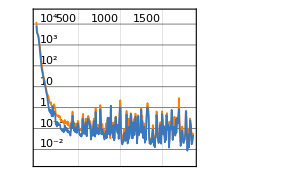
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9316  rounds:1863  time:31s  examples/s:19858
data | ,,  training examples:300  validation examples:60  processed examples:596224  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:8.15×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

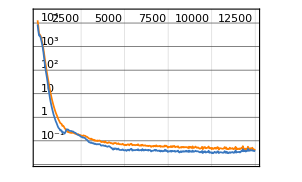
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.4min  examples/s:10375
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.5×10^-2
validation | ,,  loss:2.93×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,LearningRate->.0001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm30[[;;,2]]
```

{-19/2,-27,-59/2,-65/2,-69/2,-79/2,-44,-89/2,-97/2,-109/2,-66,-74,-165/2,-86,-99,-199/2,-102,-106,-231/2,-239/2,-241/2,-269/2,-136,-273/2,-141,-297/2,-303/2,-153,-154,-162,-325/2,-329/2,-167,-341/2,-175,-353/2,-355/2,-183,-187,-381/2}

```mathematica
testpred = wNet/@testdatanorm30[[;;,1]]
```

{-9.52103,-26.9979,-29.4777,-32.4316,-34.533,-39.4912,-44.0199,-44.5134,-48.4781,-54.5122,-66.183,-73.8761,-82.6136,-86.2296,-98.6488,-99.2086,-101.957,-106.184,-115.446,-119.046,-119.921,-134.695,-136.236,-136.744,-141.196,-148.163,-150.803,-152.184,-153.325,-162.06,-162.583,-164.653,-167.184,-170.628,-174.894,-176.339,-177.376,-182.916,-187.039,-190.545}

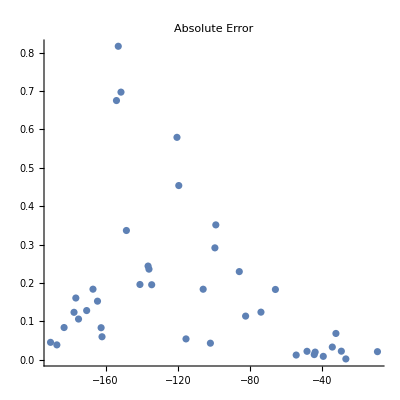

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

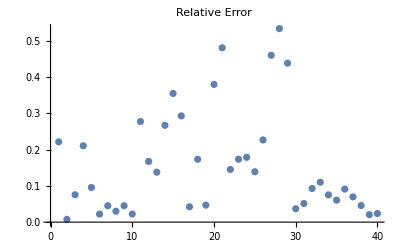

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.159219

## Real negative powers (chosen at random)

```mathematica
minweight = -300;
coeffnum=50;
datasize=500;
```

```mathematica
weights=Rationalize[SetPrecision[RandomReal[{minweight,-0.01},datasize], 4], 0];
```

```mathematica
dnexactwrandom = ParallelTable[ If[Mod[weights[[i]],12]==0,  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]}]//Normal], q]],{i,datasize}];
```

```mathematica
dnexactwrandomnorm20=Normalize/@dnexactwrandom[[;;,;;20]];
Length[dnexactwrandomnorm20]
```

500

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datapartition[Thread[dnexactwrandomnorm20->weights]];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=8500;
```

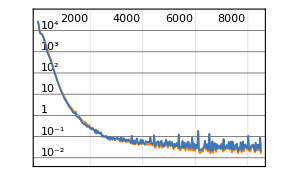
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:51000  rounds:8500  time:1.2min  examples/s:45766
data | ,,  training examples:375  validation examples:75  processed examples:3264000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.42×10^-2
validation | ,,  loss:1.89×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{-3046/11,-1745/8,-3042/11,-497/6,-299/8,-811/3,-866/7,-799/6,-4357/21,-1139/19,-233/16,-179/3,-678/7,-1011/4,-763/15,-985/6,-853/4,-279/2,-1715/9,-736/7,-793/4,-1417/7,-151/27,-1239/5,-1081/5,-1530/23,-859/6,-1109/4,-1787/20,-4229/15,-1311/5,-2553/20,-134/27,-1588/17,-1825/8,-243/4,-1491/16,-752/7,-1115/4,-666/7,-2651/13,-4178/15,-739/5,-301/4,-544/13,-1137/4,-203/19,-509/4,-667/9,-1039/4}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{-276.897,-218.034,-276.529,-82.5552,-37.3054,-270.334,-123.862,-132.946,-207.451,-59.9074,-14.5591,-59.631,-97.0301,-252.721,-51.0785,-164.011,-213.292,-139.292,-190.535,-105.146,-198.35,-202.403,-5.37989,-247.756,-216.182,-66.3861,-143.219,-277.241,-89.2658,-282.022,-262.139,-127.743,-4.86398,-93.5382,-228.142,-60.6949,-93.3068,-107.296,-278.746,-95.3076,-203.822,-278.529,-147.997,-75.3299,-42.0091,-284.406,-10.748,-127.356,-74.2008,-259.74}

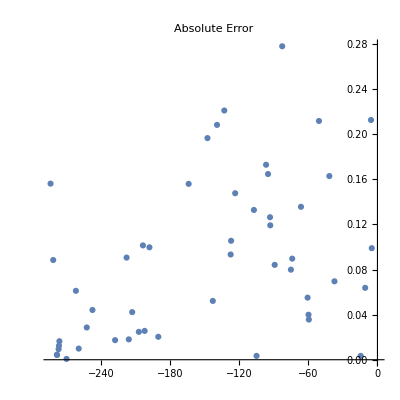

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

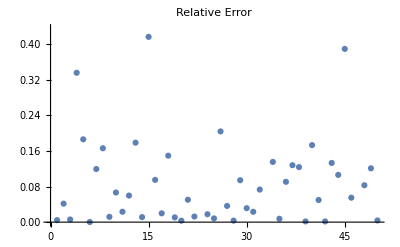

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.20917

## Half-integer positive powers

```mathematica
maxweight=200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, 1/2, maxweight,1/2}];
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
Length[dnexactw200norm30]
```

400

```mathematica
weights=Table[w,{w,1/2, maxweight,1/2}];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
enc20=enc[datanorm20]
```

NetEncoder[…]

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->enc[datanorm20],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=1000;
```

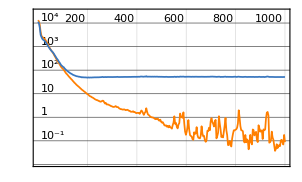
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5000  rounds:1000  time:20s  examples/s:16500
data | ,,  training examples:300  validation examples:60  processed examples:320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.1×10^-2
validation | ,,  loss:5.05×10^1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{9/2,7,14,18,19,47/2,63/2,32,36,77/2,93/2,49,119/2,63,133/2,135/2,68,74,153/2,83,173/2,87,92,195/2,103,217/2,109,115,235/2,118,129,261/2,145,160,323/2,168,337/2,182,375/2,399/2}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{32.7495,40.4468,13.5711,18.9925,26.389,16.8142,42.3371,41.4432,35.0897,35.2522,42.1938,47.0957,62.6246,65.7443,74.8455,79.1192,78.4922,75.4566,75.1137,88.0934,74.729,70.8939,89.1665,95.0932,99.7713,87.7444,84.9917,113.78,116.326,116.764,129.223,130.823,144.673,160.032,161.667,168.951,169.486,182.432,187.001,195.445}

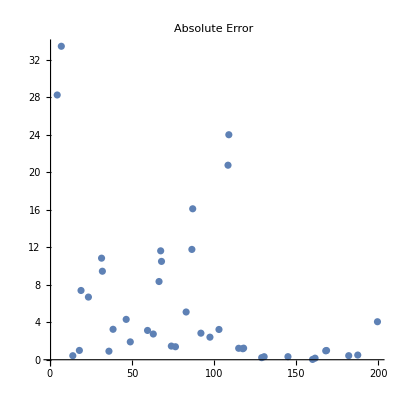

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

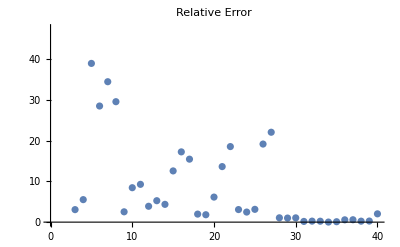

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

35.594

## Randomly chosen slice of coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
```

```mathematica
numsamp=20;
```

```mathematica
weights=Table[w,{w, -1/2, minweight, -1/2}];
```

```mathematica
randsamp=Sort[RandomSample[Range[coeffnum],numsamp]]
```

{1,4,7,9,10,13,14,16,18,19,20,21,23,25,30,32,33,41,42,48}

```mathematica
rawdata = dnexactw200[[;;,randsamp]];
normdata=Normalize/@dnexactw200[[;;,randsamp]];
Length[rawdata]
```

400

```mathematica
data=datapartition[Thread[rawdata->weights]];
datanorm=datapartition[Thread[normdata->weights]];
Length[data]
```

3

```mathematica
{traindata,valdata,testdata}=data;
{traindatanorm,valdatanorm,testdatanorm}=datanorm;
```

```mathematica
(*{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;*)
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindatanorm[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm[[1]]],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

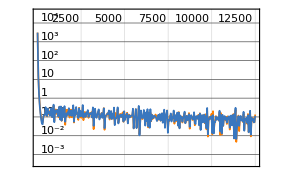
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.9min  examples/s:9709
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.3×10^-3
validation | ,,  loss:7.94×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm,All,ValidationSet->valdatanorm,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm[[;;,2]]
```

{-23/2,-22,-27,-57/2,-48,-51,-111/2,-65,-68,-151/2,-80,-165/2,-84,-89,-195/2,-101,-102,-103,-207/2,-215/2,-112,-227/2,-253/2,-127,-129,-267/2,-134,-271/2,-136,-140,-144,-309/2,-162,-167,-335/2,-337/2,-174,-355/2,-381/2,-196}

```mathematica
testpred = wNet/@testdatanorm[[;;,1]]
```

{-11.5234,-21.9508,-27.0963,-28.5272,-47.9875,-50.9815,-55.5673,-64.9612,-67.9749,-75.4755,-79.979,-82.475,-83.9846,-88.9922,-97.4766,-100.973,-101.98,-102.985,-103.486,-107.499,-112.013,-113.509,-126.507,-127.003,-128.979,-133.446,-133.939,-135.471,-135.979,-140.003,-144.01,-154.531,-161.84,-166.994,-167.503,-168.515,-174.,-177.469,-190.507,-195.988}

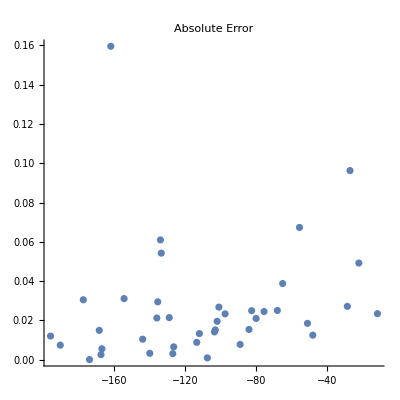

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

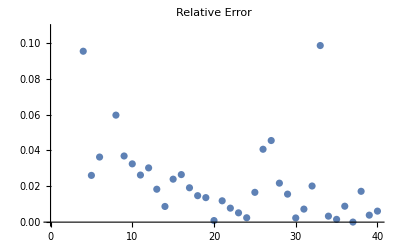

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0427851

## Mock modular forms

## Generating data for negative weights

```mathematica
minweight = -100;
coeffnum=50;
```

```mathematica
cne50w100 = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, -1/2,minweight, -1/2}];
```

```mathematica
w100 = Table[w, {w, -1/2, minweight, -1/2}];
```

## Normalized 10 coefficients

```mathematica
cne50w100norm10=Normalize/@cne50w100[[;;,;;10]];
```

```mathematica
data=MapThread[Rule,{cne10w100,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->10,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

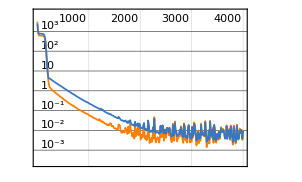
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:53452
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:2.75×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-19,-55/2,-30,-31,-45,-49,-103/2,-111/2,-57,-71,-79,-165/2,-83,-86,-181/2,-189/2,-96}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-11.8579,-18.9686,-27.5082,-30.0013,-31.0176,-45.0016,-49.0026,-51.5023,-55.5074,-57.0019,-71.0107,-79.0108,-82.5823,-83.0482,-85.963,-90.5124,-94.4849,-95.9833}

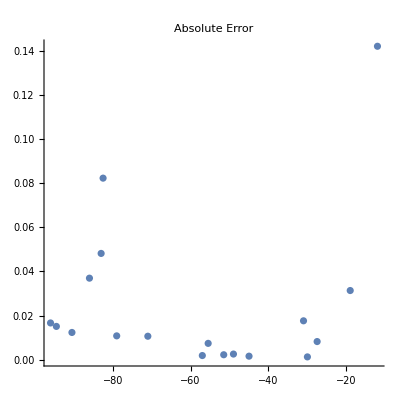

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

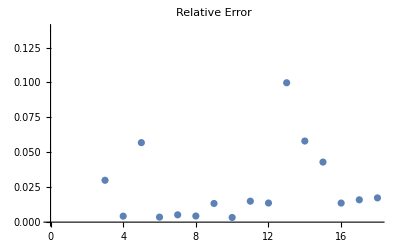

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0970438

## Normalized 30 coefficients

```mathematica
cne50w100norm30=Normalize/@cne50w100[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm30,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

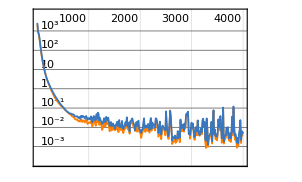
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46363
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.13×10^-4
validation | ,,  loss:5.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-4,-9/2,-10,-11,-19,-45/2,-35,-36,-41,-87/2,-49,-103/2,-62,-64,-66,-159/2,-173/2,-89,-181/2,-91}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-4.01904,-4.50736,-9.99175,-10.9861,-18.9724,-22.478,-34.9868,-35.9882,-40.9995,-43.4913,-48.993,-51.4901,-61.9679,-64.0045,-65.9944,-79.508,-86.5306,-89.0009,-90.4528,-90.9761}

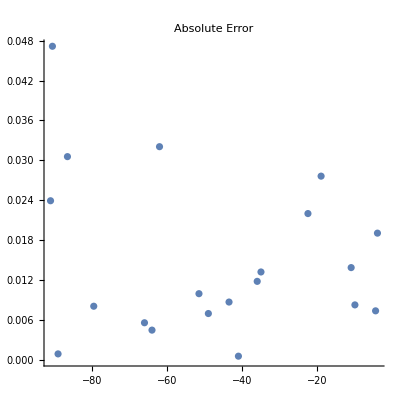

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

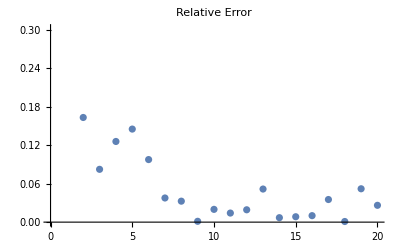

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0704135

## 30 coefficients starting at 11th coefficient

```mathematica
cne50w100norm11to40=Normalize/@cne50w100[[;;,11;;40]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm11to40,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

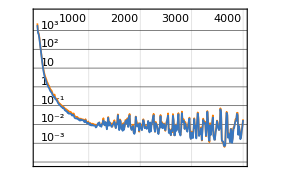
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:45839
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.86×10^-3
validation | ,,  loss:2.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-1,-17/2,-19/2,-13,-29/2,-39/2,-45/2,-25,-51/2,-65/2,-33,-71/2,-43,-44,-61,-123/2,-71,-187/2,-94,-199/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-0.984623,-8.48011,-9.48186,-12.9901,-14.5167,-19.476,-22.4832,-24.9928,-25.4965,-32.5007,-32.9923,-35.4475,-43.0156,-44.003,-61.0033,-61.5056,-70.9836,-93.4771,-93.9854,-99.4147}

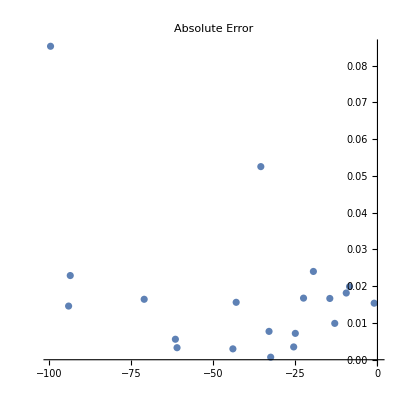

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

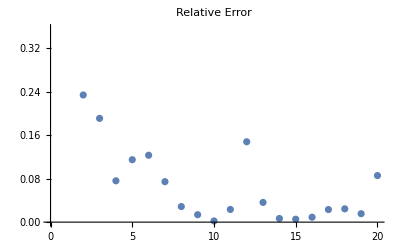

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.138669

## Generating data for positive weights

```mathematica
maxweight = 100;
coeffnum=50;
```

```mathematica
cne50w100plus = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, 0,maxweight,1/2}];
```

```mathematica
w100plus = Table[w, {w, 0,maxweight,1/2}];
```

## Normalized 30 coefficients

```mathematica
cne50w100plusnorm30=Normalize/@cne50w100plus[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100plusnorm30,w100plus}];
datasize=Length[data]
```

201

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=6000;
```

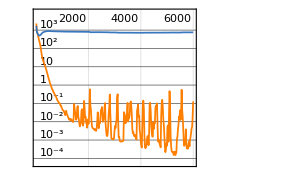
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:18000  rounds:6000  time:37s  examples/s:31805
data | ,,  training examples:150  validation examples:30  processed examples:1152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.91×10^-1
validation | ,,  loss:7.44×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]];
testpred = wNet/@testdata[[;;,1]];
```

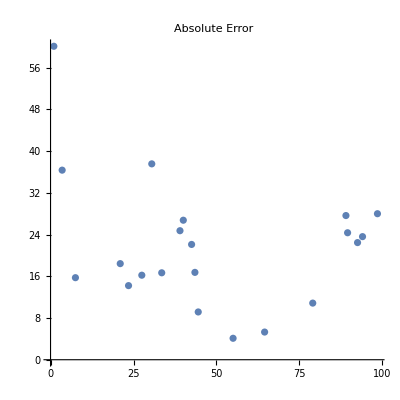

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

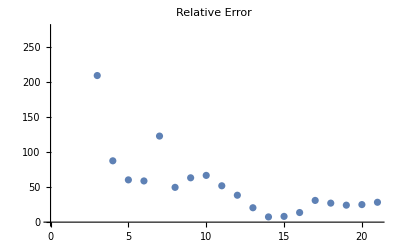

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

383.266

## Coefficients calculated via Kloosterman sums

```mathematica
minweight = -100;
coeffnum=30;
```

```mathematica
cn0c30w100 = Table[If[Mod[w,12]==0,Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
cn0c30w100norm30=Normalize/@cn0c30w100;
```

```mathematica
data=MapThread[Rule,{cn0c30w100norm30,wlist}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

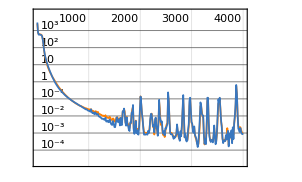
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:18s  examples/s:44348
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.83×10^-4
validation | ,,  loss:9.05×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-15,-33/2,-24,-49/2,-53/2,-29,-81/2,-83/2,-101/2,-59,-63,-147/2,-165/2,-173/2,-87,-88,-96,-100}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.9777,-16.5018,-24.0065,-24.5083,-26.4925,-29.,-40.5015,-41.5083,-50.4848,-58.9991,-62.9952,-73.4979,-82.4828,-86.4799,-86.9727,-87.9872,-96.0273,-99.8619}

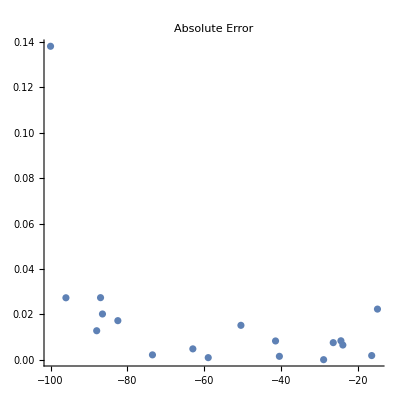

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

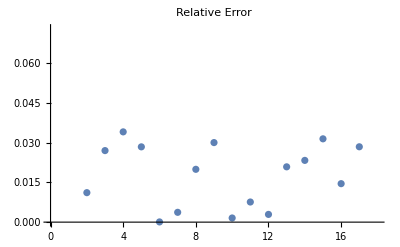

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0317603

## Comparing the real and imaginary parts of Kloosterman sums

```mathematica
minweight=-100;
coeffnum=30;
```

### Absolute values of part 1

```mathematica
cnc50w150abs1 = Table[If[Mod[w,12]==0,Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs1norm=Normalize/@cnc50w150abs1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

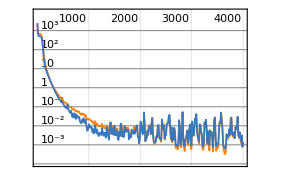
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:52883
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.18×10^-4
validation | ,,  loss:5.83×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-13,-14,-47/2,-24,-49/2,-41,-42,-44,-52,-63,-127/2,-129/2,-75,-159/2,-85,-177/2,-179/2,-195/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.9862,-13.9781,-23.553,-24.0385,-24.5241,-40.9001,-41.9487,-44.0116,-52.0027,-63.0056,-63.5005,-64.5098,-75.0047,-79.4928,-85.0017,-88.4656,-89.4739,-97.5091}

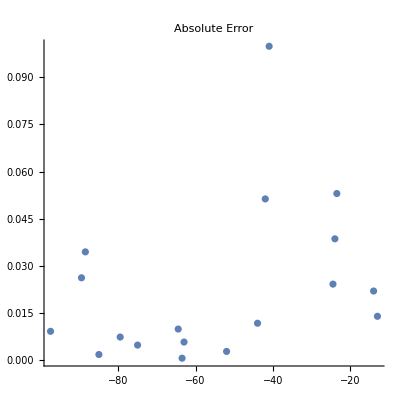

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

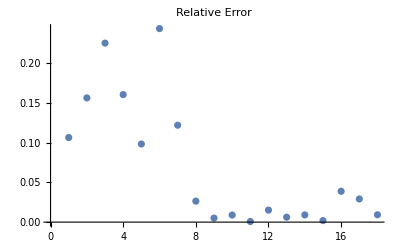

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0702341

### Real values of part 1

```mathematica
cnc50w150re1 = Table[If[Mod[w,12]==0,Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re1norm=Normalize/@cnc50w150re1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

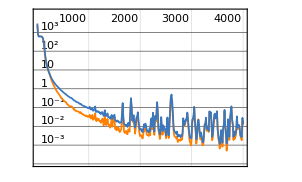
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:16s  examples/s:48043
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.8×10^-2
validation | ,,  loss:1.44×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-13,-27/2,-29/2,-43/2,-36,-45,-46,-113/2,-127/2,-64,-137/2,-75,-173/2,-93,-193/2,-97,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.3518,-17.5069,-15.584,-14.4611,-21.5254,-35.994,-45.0078,-45.9739,-56.5226,-63.519,-63.9957,-68.5148,-75.0058,-86.4915,-93.0252,-96.5665,-97.029,-98.5011}

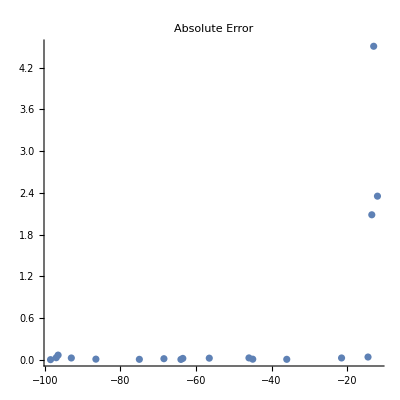

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

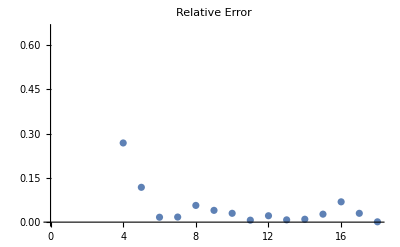

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.91242

### Absolute values of part 2

```mathematica
cnc50w150abs2 = Table[If[Mod[w,12]==0,Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs2norm=Normalize/@cnc50w150abs2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

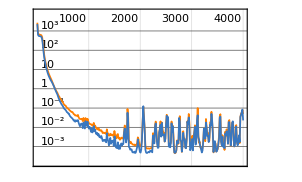
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46741
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.81×10^-2
validation | ,,  loss:4.77×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-25/2,-13,-49/2,-25,-63/2,-35,-75/2,-87/2,-101/2,-103/2,-54,-72,-73,-153/2,-86,-185/2,-187/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.2684,-12.6735,-13.0893,-24.4973,-25.0022,-31.5062,-34.9512,-37.5227,-43.4946,-50.5049,-51.5018,-54.0035,-71.998,-72.9912,-76.5007,-85.9957,-92.4892,-93.4893}

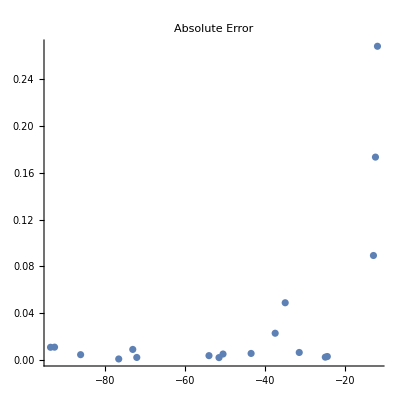

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

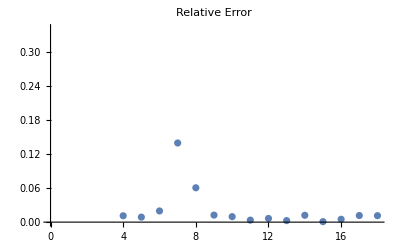

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.257055

### Real values of part 2

```mathematica
cnc50w150re2 = Table[If[Mod[w,12]==0,Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re2norm=Normalize/@cnc50w150re2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

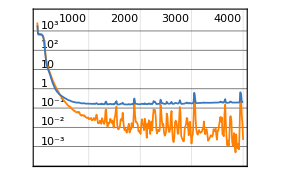
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:47423
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.93×10^-3
validation | ,,  loss:1.94×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-18,-45/2,-61/2,-65/2,-99/2,-101/2,-52,-53,-107/2,-123/2,-129/2,-133/2,-70,-75,-88,-91,-189/2,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-17.9894,-22.5604,-30.5035,-32.4917,-49.4998,-50.4841,-51.9909,-52.999,-53.4809,-61.4894,-64.4768,-66.4838,-69.9518,-74.9958,-87.9364,-91.032,-94.4711,-98.2707}

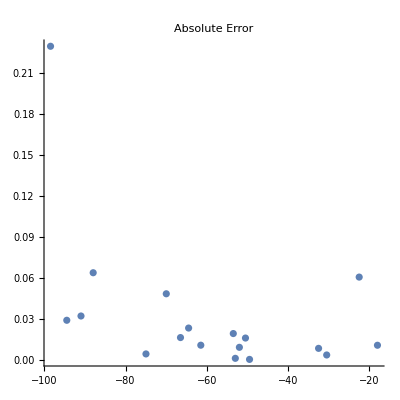

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

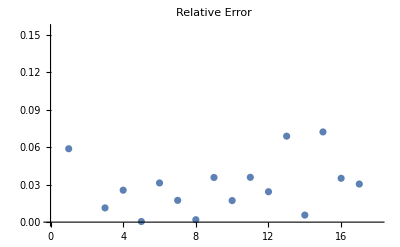

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0541437

## θ_1^k θ_2^l

0.351244 mean relative error for θ_1^m θ_2^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k20l20q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 70, 80], {k, 20}, {l, 20}];
DumpSave["t1t2k20l20q70u80mfpos1.mx", t1t2k20l20q70u80mfpos1];
```

### t1t2k20l20q70u80mfpos1, net0, 26 coeffs(r)

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

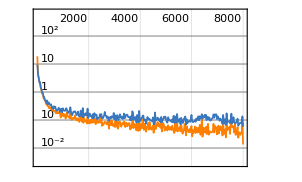
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

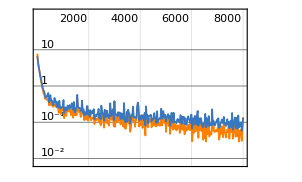
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

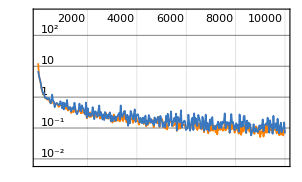
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

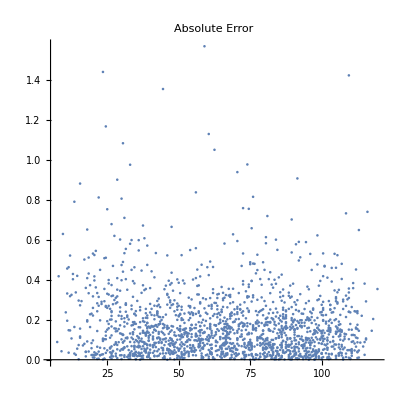

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

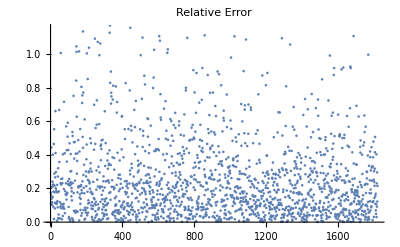

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t1t2k20l20q70u80mfpos1, net3, 26 coeffs

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k5l5q50u60mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k5l5q50u60mfneg.mx", t1t2k5l5q50u60mfneg];
t1t2k10l10q70u80mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k10l10q70u80mfneg.mx", t1t2k10l10q70u80mfneg];
```

#### t1t2k5l5q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

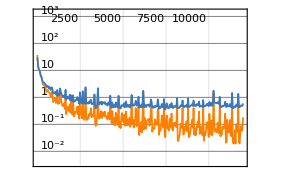
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:3.6min  examples/s:36024
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.67×10^-1
validation | ,,  loss:9.68×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

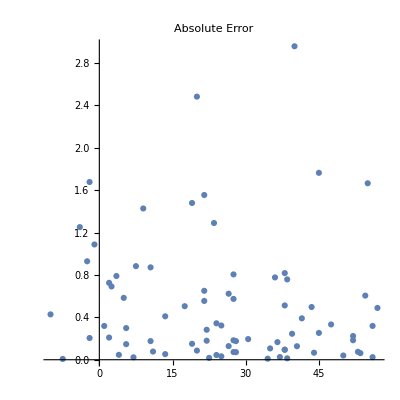

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

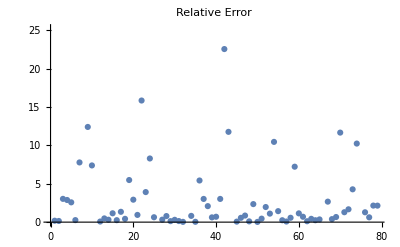

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.05481

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t1t2k5l5q50u60mfneg, Net3, 26 coeffs

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

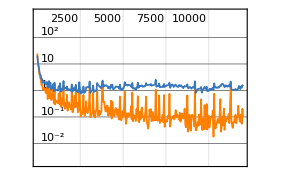
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.7min  examples/s:27360
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.22×10^-2
validation | ,,  loss:1.03
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

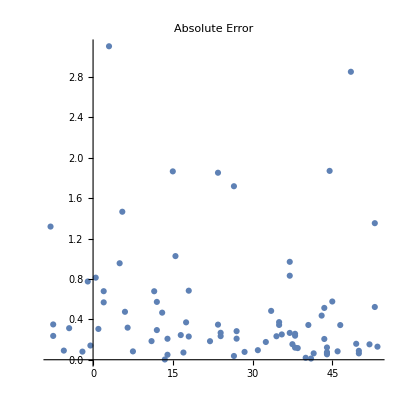

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

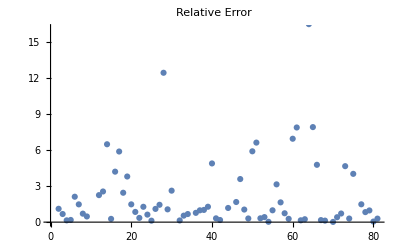

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

8.21258

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_3^m θ_4^n

0.144678 mean relative error for θ_3^m θ_4^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t3t4m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 5}, {n, 5}];
DumpSave["t3t4m5n5q70u80mfpos1.mx", t3t4m5n5q70u80mfpos1];
```

```mathematica
t3t4m20n20q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 20}, {n, 20}];
DumpSave["t3t4m20n20q70u80mfpos1.mx", t3t4m20n20q70u80mfpos1];
```

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

```mathematica
(*t3t4m20n20q30u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,30,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q30u50mfpos1.mx", t3t4m20n20q30u50mfpos1];*)
(*t3t4m20n20q50u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,50,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q50u50mfpos1.mx", t3t4m20n20q50u50mfpos1];*)
(*t3t4m20n20q70u100mfpos1 = ParallelTable[prod1pos[3,m, 4, n,70,100], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q70u100mfpos1.mx", t3t4m20n20q70u100mfpos1];*)
```

### t3t4m20n20q70u80mfpos1, net0, 35 coeffs(r)

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

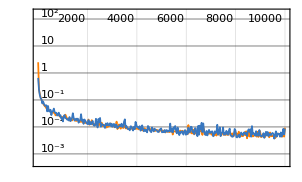
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

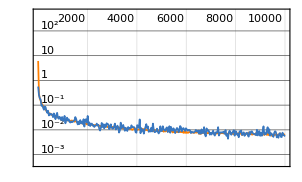
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

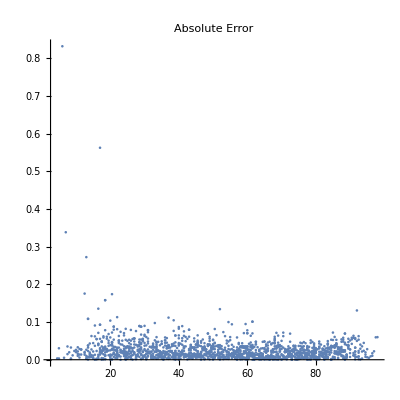

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

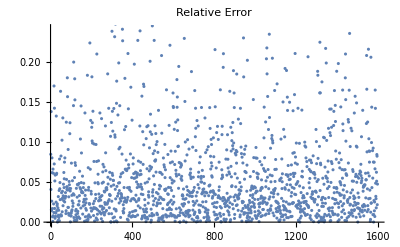

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t3t4m20n20q70u80mfpos1, net3, 35 coeffs

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*t3t4m3n3q40u50mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 40, 50], {m, -1, -3, -1}, {n, -1, -3, -1}];
DumpSave["t3t4m3n3q40u50mfneg.mx", t3t4m3n3q40u50mfneg];*)
t3t4m5n5q50u60mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 50, 60], {m, -1, -5, -1}, {n, -1, -5, -1}];
DumpSave["t3t4m5n5q50u60mfneg.mx", t3t4m5n5q50u60mfneg];
```

#### t3t4m5n5q50u60mfneg, Net0, 25 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

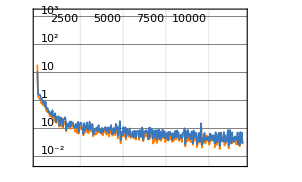
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:3.4min  examples/s:33696
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.41×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

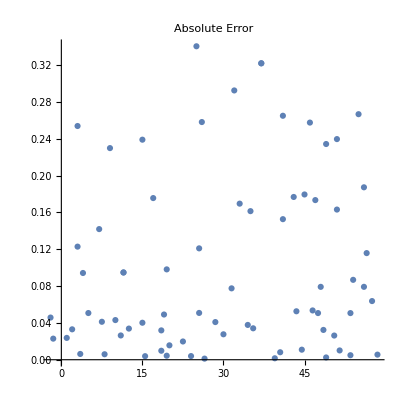

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

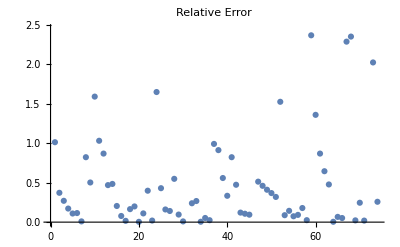

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.66833

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 25 coeffs(r)

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

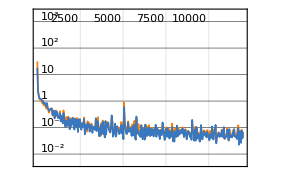
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:5.4min  examples/s:21228
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.88×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

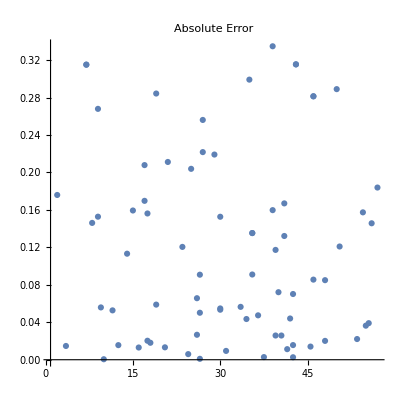

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

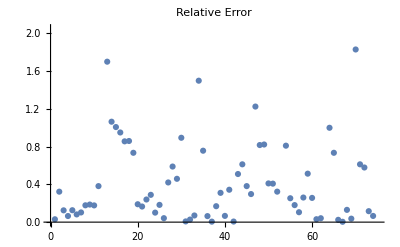

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.666275

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net0, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

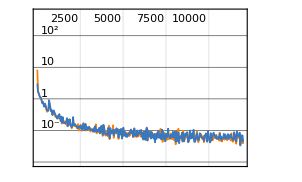
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:5.8min  examples/s:17778
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:3.47×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

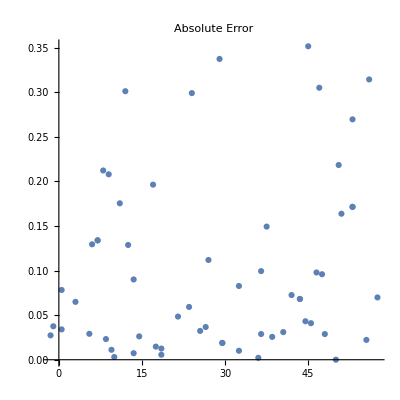

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

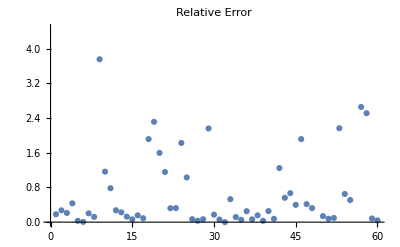

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.992729

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

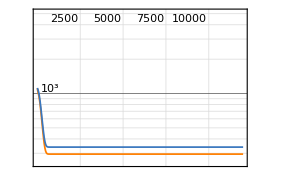
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:8.1min  examples/s:12612
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^2
validation | ,,  loss:3.39×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

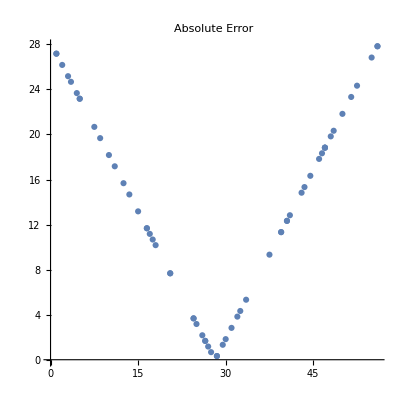

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

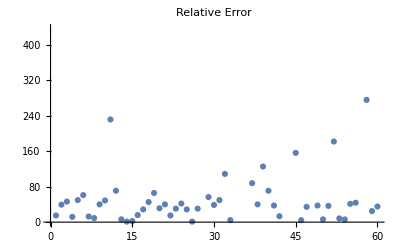

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

204.762

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_1^k θ_2^l θ_3^m θ_4^n

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, m, 4, n, 70, 80], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q70u80mfpos1, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,31,34,35,53,56,58,59,60,62,67,68,69,70}

```mathematica
data = datadefn[rawdata, 53];
```

```mathematica
datasize = Length[data]
```

19598

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4, Ramp 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

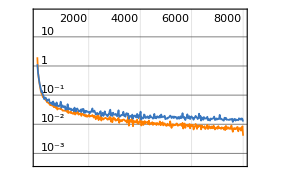
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1088000  rounds:8000  time:30min  examples/s:39097
data | ,,  training examples:8700  validation examples:1740  processed examples:69632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.14×10^-3
validation | ,,  loss:1.88×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

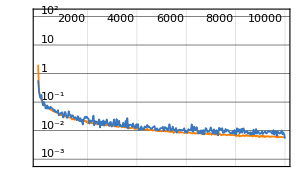
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2300000  rounds:10000  time:2.6h  examples/s:15984
data | ,,  training examples:14698  validation examples:2940  processed examples:147200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.88×10^-3
validation | ,,  loss:3.31×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 53 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

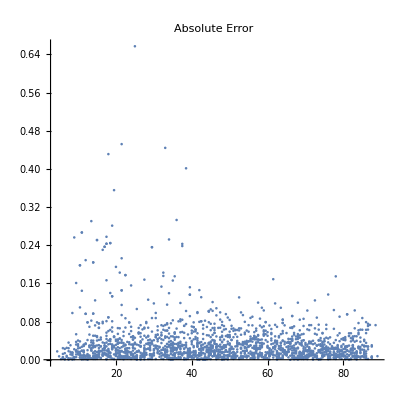

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

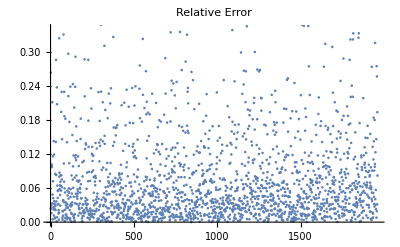

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.110949

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

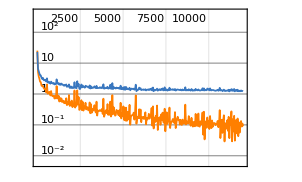
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:2.1h  examples/s:3498
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:1.44
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

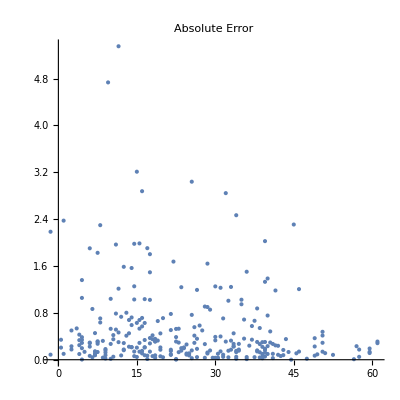

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

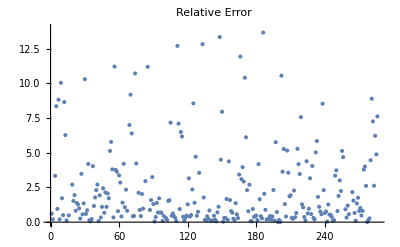

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.1182

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

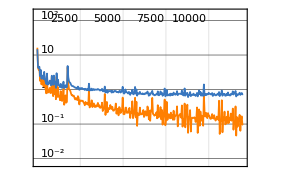
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:13min  examples/s:32683
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.66×10^-2
validation | ,,  loss:6.2×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

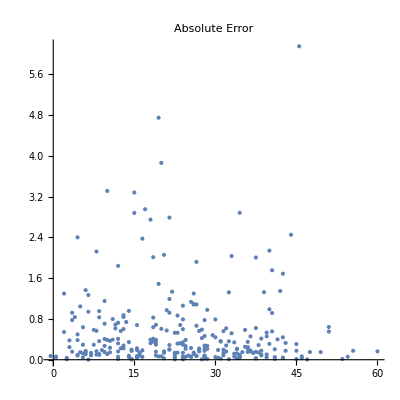

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

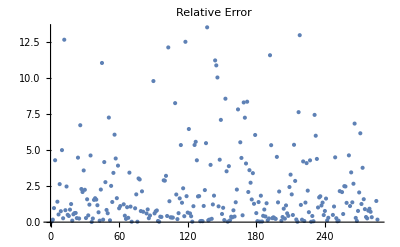

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.88915

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q20u30mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,20,30], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q20u30mfneg.mx", tallk2l2m2n2q20u30mfneg];
tallk2l2m2n2q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg.mx", tallk2l2m2n2q40u50mfneg];*)
tallk2l2m2n2q50u60mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,50,60], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q50u60mfneg.mx", tallk2l2m2n2q50u60mfneg];
(*tallk3l3m3n3q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-3, -1},{l,0,-3, -1}, {m,0,-3, -1}, {n,0,-3, -1}];
DumpSave["tallk3l3m3n3q40u50mfneg.mx", tallk3l3m3n3q40u50mfneg];*)
```

#### tallk2l2m2n2q40u50mfneg, Net0, 40 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

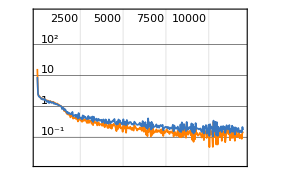
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:6.3min  examples/s:34565
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.78×10^-2
validation | ,,  loss:8.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

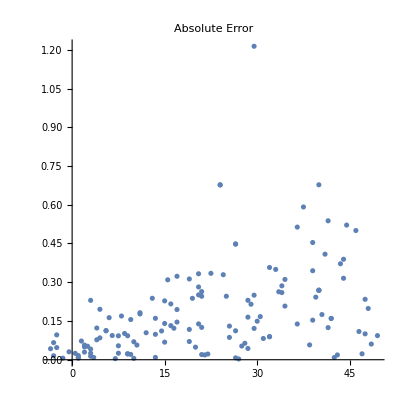

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

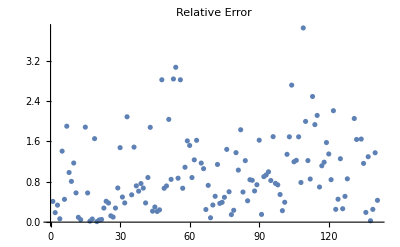

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.14707

#### tallk2l2m2n2q40u50mfneg, Net3, 40 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

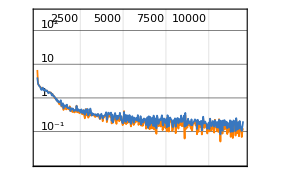
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:7.0min  examples/s:30924
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:1.16×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

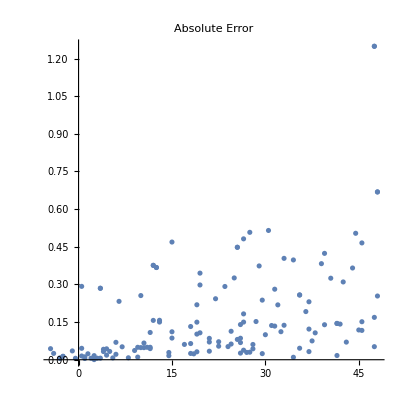

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

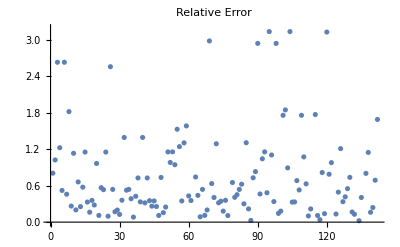

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.36787

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
(*plist=klmnneg[5, 400];*)
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn-neg, Net0, 36 coeffs(r)

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[3525]] // N
```

{4.27264×10^-7,4.20954×10^-6,0.0000224917,0.0000908428,0.000315714,0.000991569,0.00287415,0.00780589,0.0201089,0.0495152,0.148638,-8.12796,1166.62,-95597.4,5.11654×10^6,-1.92659×10^8,5.4057×10^9,-1.18237×10^11,2.08989×10^12,-3.07319×10^13,3.85001×10^14,-4.19022×10^15,4.0269×10^16,-3.46398×10^17,2.698×10^18,-1.92137×10^19,1.2616×10^20,-7.6932×10^20,4.38424×10^21,-2.34781×10^22,1.18715×10^23,-5.69206×10^23,2.59778×10^24,-1.13232×10^25,4.72812×10^25,-1.89646×10^26}→40.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

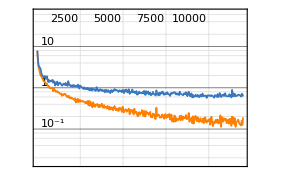
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:45min  examples/s:23936
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:7.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

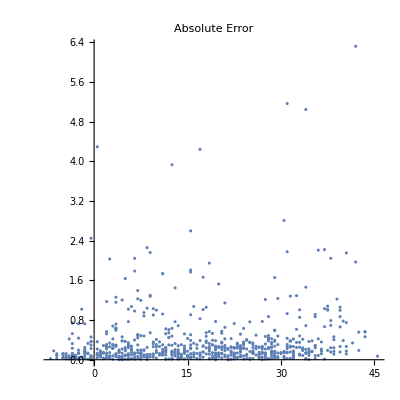

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

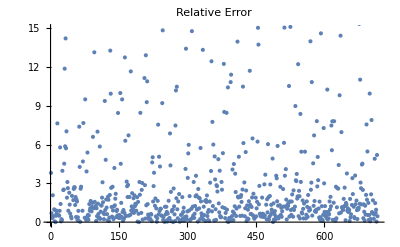

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

6.31506

#### jacobi-klmn-neg, Net3, 36 coeffs

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

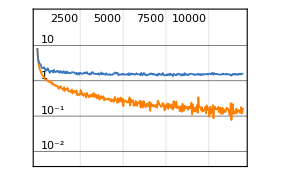
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:1.3h  examples/s:13916
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.02×10^-2
validation | ,,  loss:1.41
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

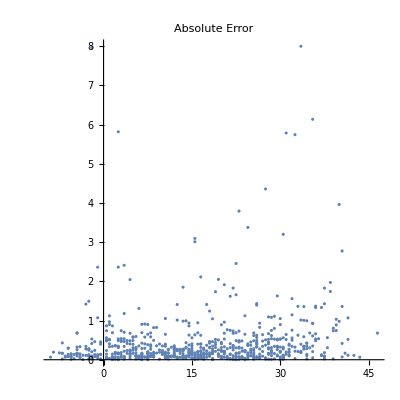

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

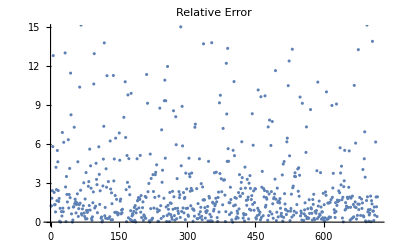

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.08278

## θ_1^k θ_2^l θ_3^m θ_4^n/Δ

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q50u60mfpos0 = ParallelTable[Quiet @ allprodθbyΔ[1,k, 2, l, 3, m, 4, n, 50, 60, 0], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
DumpSave["tallk5l5m5n5q50u60mfpos0.mx", tallk5l5m5n5q50u60mfpos0];
```

#### tallk5l5m5n5q50u60mfpos0, Net0, 25 coeffs(r)

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

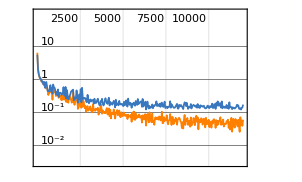
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2568000  rounds:12000  time:2.1h  examples/s:21238
data | ,,  training examples:13679  validation examples:2736  processed examples:164352000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.54×10^-1
validation | ,,  loss:6.4×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

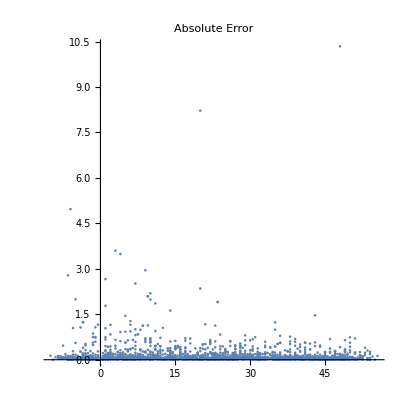

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

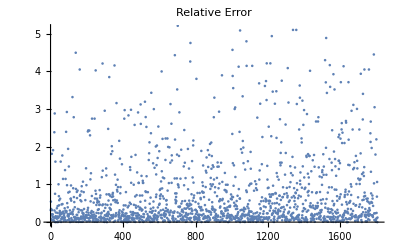

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.78562

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

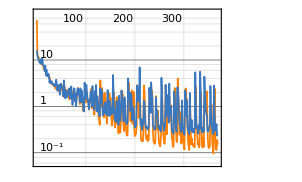
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:79027  rounds:369  time:5.7min  examples/s:14848
data | ,,  training examples:13679  validation examples:2736  processed examples:5057728  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.52×10^-1
validation | ,,  loss:2.47×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{16.0926,11.9417,12.7808,10.7139,10.5111,8.93514,8.706,9.56276,7.48489,10.4442,8.14548,10.7495,6.95333,9.13793,7.72118,6.81918,5.72008,7.03171,8.11831,4.67765,6.18557,4.44467,4.67148,6.18168,3.94506,4.71163,3.21388,3.66859,3.99813,2.9964,3.1201,3.40314,3.15504,2.72024,3.18338,2.82781,2.99386,2.70992,2.98149,4.71385,2.77414,3.00927,2.18779,2.76448,2.61506,2.12827,2.93845,1.77033,2.83599,1.67607,4.50406,2.71944,2.47134,2.14134,1.63109,2.69921,4.55554,1.91445,1.48809,2.25025,1.58571,2.15713,1.57429,1.99194,1.8526,2.90508,1.99093,1.80389,1.4765,1.53903,2.69787,2.04037,1.2148,1.0722,1.77905,1.54136,2.30208,2.61964,1.28543,1.8712,1.00941,2.37994,0.902768,2.35197,2.4627,1.80541,2.02093,1.08538,1.37369,2.43975,1.22857,2.20887,1.98397,1.36891,1.34718,0.839483,0.77669,0.808365,5.701,1.41746,2.40846,2.89852,1.8324,0.687148,1.84173,1.3877,0.869494,1.28626,0.778902,2.09805,2.08162,1.32737,0.982693,1.40927,4.05842,1.23398,1.4557,0.834442,2.15352,1.87722,0.838156,2.88944,0.775091,1.63078,1.89756,0.657817,0.774783,0.667926,0.612098,2.47978,1.49285,0.940459,2.25303,1.17497,0.639982,0.52118,0.994008,1.01972,0.714663,1.23232,1.56942,0.547212,0.649391,0.64335,2.2404,1.24647,0.918884,1.71444,0.620284,1.29436,0.667836,1.24048,0.633874,0.683968,0.720698,4.75539,2.48478,1.129,0.661845,0.501406,0.83661,0.469502,1.37691,1.23815,0.618178,0.513137,0.396855,2.41645,0.968578,0.506419,0.486792,0.72617,1.40826,2.96528,1.37715,1.36421,0.480305,0.480042,0.419483,2.73064,0.739148,0.484611,0.433849,0.41813,0.403046,0.475134,4.00832,1.54767,3.04069,0.988029,1.11156,0.776653,1.92374,1.25709,0.472821,0.538992,0.962304,0.917579,0.491703,0.356179,0.343321,0.435686,0.384582,1.34313,2.7927,2.82787,1.61048,1.30312,1.37397,6.94818,0.628673,0.422697,0.381513,0.531699,0.310958,0.382031,0.44538,0.412753,1.31918,1.16619,0.540989,0.514693,0.343317,0.360958,0.367236,0.314876,0.324899,0.340877,0.349714,2.50361,1.42139,1.03089,0.417355,3.29193,1.95176,1.41899,0.42506,0.322963,0.365225,0.315203,0.31448,0.34471,2.17267,0.966683,0.667695,0.802847,0.555018,0.407986,0.279674,0.384187,0.310248,0.391725,0.289416,0.549491,7.70718,1.65149,0.424256,0.421447,0.302143,0.30202,0.320151,0.386696,2.91529,0.750104,0.434534,0.769269,0.925066,1.77453,0.445621,4.79508,1.38226,0.901007,0.664683,0.988947,0.348633,0.316028,0.296406,0.274686,0.257373,0.380953,3.8014,1.6019,0.502469,0.351612,0.285675,0.327076,4.72541,2.57843,1.5997,0.674357,0.385859,0.446572,0.379513,0.289148,0.278758,2.00972,0.691886,0.327127,0.337194,0.272207,0.243914,0.405941,3.9943,1.96126,0.622385,1.33053,0.437016,0.304258,0.301545,0.288492,0.251765,3.04475,0.843812,0.400923,0.303276,0.514034,0.275643,0.232961,0.350032,0.322863,0.270921,0.373931,2.45135,8.35501,0.945073,0.336518,0.371196,0.421567,0.281015,0.259408,0.399217,0.319492,5.6113,2.19203,1.92803,0.368692,0.272372,0.279473,0.433919,0.259159,0.28881,4.38355,1.79571,0.743435,1.41533,0.694694,0.671538,0.302792,0.283755,0.301587,0.30221,0.360578,0.377448,2.75124,1.27086,0.496083,0.437406,0.311006,0.252385,0.231329,0.293349,2.80962,0.575492,0.299476,0.309908,0.240181,0.58681,0.234391,0.247358}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

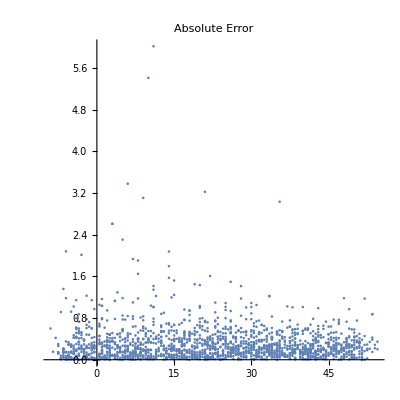

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

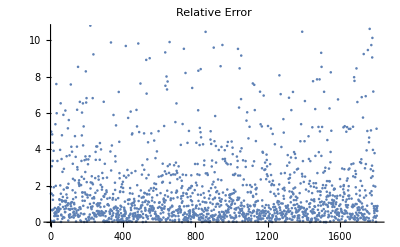

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.53036

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net0, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

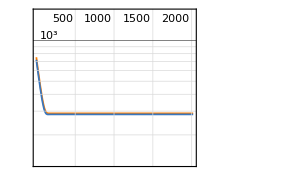
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:345279  rounds:2019  time:10min  examples/s:35890
data | ,,  training examples:10942  validation examples:2189  processed examples:22097856  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^2
validation | ,,  loss:2.84×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{752.842,745.539,738.317,731.197,724.129,717.129,710.237,703.386,696.626,689.912,683.287,676.724,670.235,663.81,657.419,651.125,644.894,638.715,632.595,626.557,620.538,614.612,608.734,602.91,597.156,591.444,585.808,580.215,574.688,569.208,563.785,558.419,553.111,547.857,542.671,537.525,532.426,527.4,522.425,517.507,512.635,507.825,503.08,498.376,493.733,489.136,484.592,480.101,475.681,471.291,466.97,462.72,458.502,454.347,450.24,446.196,442.186,438.24,434.37,430.533,426.754,423.012,419.35,415.725,412.151,408.638,405.179,401.759,398.416,395.121,391.871,388.674,385.52,382.446,379.405,376.416,373.479,370.601,367.759,364.991,362.257,359.581,356.962,354.4,351.863,349.399,346.999,344.626,342.307,340.04,337.815,335.656,333.543,331.48,329.46,327.504,325.578,323.716,321.908,320.132,318.414,316.73,315.11,313.549,312.009,310.527,309.077,307.697,306.359,305.056,303.821,302.607,301.433,300.327,299.252,298.216,297.219,296.279,295.387,294.519,293.698,292.915,292.176,291.469,290.803,290.183,289.586,289.031,288.517,288.025,287.564,287.141,286.753,286.394,286.063,285.758,285.475,285.214,284.995,284.787,284.598,284.43,284.285,284.157,284.04,283.942,283.857,283.788,283.727,283.677,283.636,283.604,283.579,283.56,283.547,283.538,283.534,283.532,283.534,283.539,283.543,283.551,283.56,283.57,283.58,283.591,283.602,283.611,283.621,283.63,283.643,283.651,283.661,283.672,283.68,283.693,283.698,283.705,283.715,283.721,283.724,283.732,283.739,283.747,283.75,283.751,283.762,283.764,283.768,283.771,283.778,283.777,283.781,283.782,283.783,283.786,283.79,283.792,283.791,283.795,283.795,283.796,283.798,283.799,283.802,283.803,283.805,283.804,283.803,283.81,283.807,283.808,283.81,283.809,283.812,283.81,283.811,283.811,283.814,283.812,283.811,283.814,283.815,283.811,283.815,283.813,283.817,283.817,283.817,283.816,283.815,283.822,283.815,283.817,283.817,283.818,283.815,283.818,283.816,283.819,283.816,283.816,283.82,283.817,283.818,283.819,283.818,283.819,283.816,283.815,283.818,283.814,283.817,283.818,283.816,283.813,283.818,283.818,283.815,283.818,283.821,283.82,283.813,283.819,283.819,283.82,283.818,283.818,283.819,283.818,283.818,283.816,283.814,283.822,283.817,283.822,283.818,283.819,283.816,283.818,283.82,283.817,283.82,283.82,283.82,283.822,283.821,283.816,283.816,283.819,283.817,283.815,283.818,283.815,283.82,283.819,283.819,283.818,283.823,283.82,283.818,283.814,283.815,283.818,283.816,283.82,283.821,283.818,283.819,283.815,283.819,283.82,283.819,283.821,283.82,283.817,283.817,283.818,283.815,283.819,283.824,283.817,283.819,283.818,283.816,283.821,283.82,283.817,283.819,283.819,283.818,283.82,283.819,283.816,283.816,283.816,283.819,283.817,283.82,283.818,283.818,283.817,283.821,283.819,283.823,283.821,283.819,283.817,283.822,283.82,283.817,283.82,283.82,283.82,283.816,283.819,283.821,283.818,283.818,283.817,283.817,283.814,283.818,283.816,283.817,283.818,283.82,283.815,283.822,283.823,283.817,283.819,283.819,283.816,283.82,283.818,283.819,283.814,283.816,283.819,283.817,283.819,283.816,283.817,283.816,283.82,283.816,283.817,283.818,283.818,283.819,283.819,283.82,283.819,283.816,283.816,283.815,283.818,283.82,283.817,283.818,283.815,283.815,283.814,283.816,283.817,283.817,283.817,283.816,283.815,283.82,283.817,283.819,283.817,283.82,283.818,283.823,283.817,283.814,283.819,283.817,283.818,283.818,283.82,283.817,283.815,283.815,283.822,283.817,283.82,283.818,283.82,283.815,283.821,283.82,283.817,283.817,283.818,283.818,283.819,283.817,283.82,283.817,283.817,283.818,283.821,283.817,283.817,283.818,283.818,283.818,283.817,283.813,283.816,283.82,283.821,283.82,283.819,283.825,283.817,283.82,283.821,283.818,283.819,283.818,283.818,283.819,283.818,283.818,283.818,283.821,283.818,283.818,283.819,283.816,283.817,283.818,283.818,283.817,283.818,283.821,283.821,283.813,283.817,283.82,283.815,283.818,283.819,283.818,283.816,283.819,283.819,283.818,283.819,283.816,283.818,283.817,283.818,283.817,283.819,283.816,283.817,283.817,283.818,283.818,283.817,283.821,283.818,283.817,283.82,283.819,283.819,283.821,283.819,283.817,283.814,283.816,283.816,283.818,283.818,283.818,283.818,283.819,283.814,283.819,283.814,283.817,283.815,283.817,283.819,283.815,283.814,283.819,283.812,283.821,283.819,283.818,283.817,283.818,283.82,283.821,283.819,283.816,283.819,283.817,283.814,283.816,283.818,283.822,283.821,283.815,283.818,283.818,283.816,283.82,283.82,283.82,283.818,283.82,283.82,283.818,283.821,283.816,283.822,283.817,283.818,283.821,283.819,283.819,283.819,283.818,283.818,283.816,283.823,283.819,283.817,283.815,283.816,283.82,283.818,283.82,283.817,283.816,283.817,283.815,283.819,283.82,283.818,283.817,283.821,283.819,283.821,283.819,283.818,283.818,283.817,283.817,283.815,283.82,283.816,283.818,283.82,283.818,283.82,283.82,283.816,283.817,283.821,283.82,283.817,283.82,283.818,283.819,283.82,283.819,283.819,283.817,283.813,283.817,283.82,283.818,283.818,283.822,283.818,283.819,283.82,283.819,283.819,283.817,283.817,283.818,283.819,283.818,283.818,283.819,283.818,283.82,283.822,283.816,283.82,283.82,283.818,283.819,283.817,283.819,283.817,283.818,283.817,283.819,283.819,283.82,283.82,283.817,283.814,283.821,283.822,283.821,283.82,283.819,283.819,283.818,283.82,283.819,283.818,283.817,283.815,283.82,283.818,283.819,283.817,283.822,283.817,283.817,283.82,283.818,283.821,283.82,283.819,283.818,283.819,283.815,283.819,283.818,283.816,283.819,283.82,283.817,283.817,283.817,283.815,283.819,283.82,283.818,283.82,283.819,283.819,283.818,283.819,283.815,283.816,283.819,283.816,283.819,283.815,283.818,283.817,283.813,283.816,283.816,283.815,283.816,283.815,283.82,283.819,283.818,283.824,283.817,283.819,283.823,283.818,283.818,283.817,283.82,283.821,283.821,283.815,283.82,283.822,283.818,283.821,283.821,283.82,283.817,283.816,283.818,283.823,283.818,283.817,283.819,283.817,283.818,283.817,283.818,283.82,283.819,283.82,283.823,283.817,283.816,283.818,283.82,283.822,283.82,283.818,283.82,283.82,283.819,283.82,283.819,283.818,283.817,283.817,283.82,283.816,283.82,283.813,283.82,283.82,283.818,283.813,283.821,283.817,283.818,283.821,283.818,283.816,283.818,283.815,283.819,283.818,283.817,283.821,283.817,283.814,283.82,283.821,283.818,283.82,283.817,283.814,283.821,283.817,283.818,283.816,283.816,283.816,283.82,283.817,283.818,283.823,283.816,283.818,283.817,283.816,283.815,283.817,283.817,283.82,283.818,283.815,283.82,283.816,283.82,283.82,283.82,283.815,283.814,283.818,283.819,283.815,283.813,283.817,283.819,283.819,283.818,283.82,283.818,283.816,283.815,283.817,283.818,283.816,283.819,283.818,283.817,283.814,283.816,283.815,283.817,283.819,283.818,283.818,283.814,283.817,283.818,283.816,283.816,283.815,283.82,283.821,283.818,283.818,283.816,283.817,283.821,283.819,283.817,283.821,283.817,283.82,283.822,283.819,283.816,283.817,283.818,283.82,283.821,283.817,283.818,283.818,283.817,283.815,283.817,283.818,283.818,283.817,283.82,283.819,283.821,283.817,283.819,283.821,283.82,283.818,283.82,283.818,283.816,283.817,283.818,283.818,283.82,283.818,283.823,283.814,283.819,283.819,283.817,283.818,283.817,283.816,283.818,283.817,283.817,283.818,283.819,283.816,283.816,283.816,283.817,283.814,283.816,283.819,283.816,283.819,283.813,283.816,283.817,283.82,283.822,283.82,283.815,283.818,283.819,283.816,283.817,283.82,283.817,283.821,283.821,283.82,283.821,283.823,283.819,283.818,283.819,283.82,283.82,283.818,283.82,283.816,283.817,283.817,283.816,283.821,283.818,283.818,283.818,283.82,283.816,283.819,283.816,283.818,283.82,283.818,283.816,283.819,283.819,283.819,283.82,283.819,283.821,283.818,283.821,283.816,283.821,283.818,283.817,283.815,283.817,283.816,283.817,283.816,283.815,283.822,283.817,283.82,283.818,283.819,283.818,283.818,283.817,283.819,283.818,283.821,283.817,283.818,283.819,283.822,283.818,283.818,283.818,283.82,283.815,283.819,283.821,283.819,283.817,283.819,283.815,283.814,283.82,283.816,283.819,283.819,283.815,283.821,283.817,283.82,283.816,283.818,283.815,283.818,283.821,283.817,283.817,283.818,283.817,283.817,283.815,283.817,283.816,283.817,283.818,283.815,283.816,283.817,283.818,283.816,283.816,283.818,283.817,283.817,283.816,283.817,283.818,283.82,283.816,283.817,283.821,283.819,283.821,283.818,283.818,283.818,283.819,283.818,283.816,283.817,283.819,283.818,283.814,283.815,283.82,283.819,283.82,283.817,283.818,283.813,283.817,283.817,283.813,283.816,283.816,283.818,283.824,283.817,283.815,283.815,283.816,283.822,283.817,283.819,283.818,283.819,283.815,283.816,283.82,283.82,283.816,283.819,283.82,283.819,283.814,283.82,283.817,283.817,283.818,283.817,283.82,283.818,283.816,283.819,283.818,283.821,283.816,283.82,283.823,283.816,283.815,283.816,283.818,283.818,283.821,283.821,283.82,283.82,283.818,283.818,283.819,283.818,283.82,283.819,283.816,283.818,283.818,283.816,283.819,283.817,283.821,283.818,283.815,283.819,283.819,283.815,283.817,283.814,283.816,283.818,283.817,283.818,283.815,283.82,283.816,283.82,283.819,283.816,283.819,283.82,283.814,283.822,283.818,283.818,283.821,283.817,283.819,283.818,283.82,283.818,283.818,283.819,283.818,283.818,283.818,283.819,283.818,283.82,283.816,283.818,283.821,283.818,283.817,283.815,283.814,283.819,283.815,283.814,283.82,283.815,283.818,283.815,283.818,283.818,283.82,283.817,283.818,283.821,283.82,283.816,283.817,283.818,283.819,283.816,283.818,283.819,283.818,283.821,283.817,283.818,283.817,283.819,283.817,283.817,283.817,283.819,283.817,283.817,283.821,283.814,283.816,283.817,283.819,283.82,283.819,283.817,283.817,283.821,283.816,283.818,283.817,283.82,283.819,283.821,283.817,283.823,283.822,283.818,283.821,283.819,283.821,283.818,283.819,283.819,283.818,283.816,283.816,283.82,283.819,283.817,283.82,283.821,283.817,283.817,283.819,283.818,283.816,283.816,283.819,283.816,283.817,283.82,283.817,283.816,283.816,283.818,283.816,283.821,283.818,283.815,283.818,283.816,283.816,283.817,283.815,283.818,283.817,283.82,283.819,283.82,283.816,283.819,283.821,283.816,283.819,283.818,283.815,283.817,283.818,283.815,283.818,283.816,283.818,283.815,283.816,283.814,283.816,283.816,283.816,283.816,283.816,283.816,283.817,283.817,283.821,283.818,283.818,283.821,283.823,283.817,283.818,283.819,283.819,283.816,283.819,283.819,283.817,283.811,283.82,283.816,283.819,283.818,283.82,283.819,283.82,283.819,283.82,283.819,283.82,283.818,283.82,283.818,283.818,283.819,283.816,283.816,283.818,283.819,283.816,283.813,283.819,283.815,283.816,283.819,283.815,283.819,283.818,283.819,283.815,283.821,283.816,283.822,283.814,283.821,283.816,283.822,283.817,283.819,283.822,283.817,283.816,283.82,283.821,283.82,283.819,283.822,283.818,283.819,283.819,283.817,283.818,283.816,283.82,283.821,283.818,283.821,283.819,283.819,283.818,283.817,283.822,283.816,283.817,283.816,283.815,283.815,283.817,283.819,283.82,283.819,283.818,283.82,283.816,283.819,283.819,283.819,283.815,283.818,283.817,283.818,283.821,283.817,283.817,283.82,283.819,283.821,283.818,283.82,283.819,283.819,283.815,283.816,283.816,283.817,283.817,283.815,283.822,283.82,283.818,283.816,283.821,283.816,283.818,283.817,283.816,283.816,283.819,283.815,283.817,283.818,283.817,283.821,283.813,283.821,283.818,283.819,283.82,283.819,283.817,283.819,283.821,283.821,283.824,283.821,283.816,283.819,283.82,283.815,283.819,283.816,283.815,283.817,283.817,283.817,283.818,283.821,283.82,283.819,283.818,283.819,283.819,283.818,283.817,283.815,283.819,283.816,283.82,283.814,283.819,283.818,283.817,283.819,283.819,283.823,283.82,283.818,283.816,283.818,283.82,283.816,283.816,283.82,283.814,283.819,283.82,283.816,283.817,283.818,283.819,283.819,283.815,283.815,283.818,283.817,283.817,283.817,283.819,283.818,283.816,283.816,283.821,283.819,283.818,283.816,283.818,283.818,283.819,283.82,283.816,283.814,283.82,283.815,283.818,283.819,283.817,283.817,283.818,283.819,283.816,283.818,283.816,283.817,283.817,283.816,283.815,283.819,283.814,283.821,283.816,283.818,283.819,283.816,283.817,283.817,283.819,283.818,283.818,283.816,283.818,283.815,283.818,283.82,283.817,283.819,283.819,283.82,283.816,283.818,283.817,283.816,283.821,283.816,283.818,283.821,283.817,283.813,283.815,283.817,283.817,283.821,283.818,283.817,283.815,283.817,283.818,283.818,283.816,283.815,283.816,283.817,283.816,283.819,283.816,283.819,283.819,283.816,283.814,283.819,283.818,283.818,283.813,283.816,283.813,283.82,283.818,283.823,283.817,283.818,283.817,283.817,283.819,283.818,283.822,283.814,283.817,283.819,283.817,283.818,283.818,283.817,283.815,283.817,283.82,283.818,283.817,283.821,283.82,283.819,283.817,283.817,283.818,283.814,283.819,283.819,283.819,283.816,283.819,283.818,283.82,283.82,283.818,283.819,283.818,283.818,283.815,283.817,283.818,283.815,283.82,283.817,283.818,283.819,283.816,283.82,283.819,283.817,283.817,283.817,283.817,283.819,283.814,283.821,283.818,283.821,283.819,283.819,283.819,283.822,283.819,283.819,283.819,283.821,283.818,283.819,283.816,283.817,283.821,283.82,283.821,283.817,283.818,283.818,283.819,283.822,283.82,283.817,283.818,283.819,283.822,283.816,283.818,283.819,283.819,283.821,283.814,283.815,283.816,283.823,283.818,283.82,283.819,283.818,283.817,283.82,283.819,283.818,283.819,283.82,283.818,283.815,283.819,283.819,283.818,283.819,283.817,283.816,283.812,283.816,283.818,283.819,283.817,283.814,283.818,283.815,283.816,283.816,283.817,283.817,283.815,283.82,283.818,283.818,283.814,283.82,283.816,283.817,283.819,283.817,283.819,283.818,283.818,283.819,283.816,283.817,283.822,283.819,283.817,283.821,283.823,283.819,283.817,283.82,283.819,283.815,283.819,283.818,283.817,283.817,283.816,283.814,283.819,283.821,283.815,283.818,283.818,283.819,283.818,283.817,283.816,283.819,283.814,283.816,283.817,283.819,283.819,283.817,283.816,283.818,283.819,283.818,283.818,283.815,283.819,283.819,283.818,283.818,283.82,283.818,283.816,283.817,283.816,283.815,283.817,283.817,283.82,283.819,283.818,283.818,283.818,283.819,283.817,283.816,283.82,283.817,283.82,283.817,283.815,283.819,283.816,283.814,283.815,283.818,283.823,283.817,283.817,283.817,283.817,283.819,283.823,283.816,283.816,283.818,283.819,283.819,283.817,283.82,283.817,283.82,283.823,283.816,283.819,283.821,283.817,283.818,283.819,283.815,283.819,283.82,283.819,283.819,283.815,283.818,283.819,283.816,283.82,283.818,283.818,283.818,283.82,283.819,283.818,283.818,283.817,283.821,283.818,283.82,283.818,283.816,283.819,283.816,283.815,283.821,283.817,283.817,283.817,283.817,283.816,283.818,283.818,283.818,283.814,283.819,283.815,283.818,283.816,283.819,283.82,283.821,283.821,283.819,283.818,283.817,283.816,283.821,283.82,283.819,283.819,283.816,283.817,283.819,283.816,283.813,283.818,283.822,283.816,283.817,283.819,283.817,283.814,283.819,283.817,283.818,283.821,283.822,283.816,283.818,283.82,283.815,283.817,283.819,283.817,283.818,283.821,283.817,283.82,283.816,283.822,283.817,283.819,283.821,283.819,283.817,283.818,283.817,283.818,283.821,283.819,283.819,283.819,283.817,283.818,283.817,283.817,283.818,283.817,283.816,283.814,283.816,283.816,283.818,283.819,283.822,283.814,283.822,283.819,283.817,283.82,283.815,283.817,283.817,283.819,283.819,283.82,283.816,283.818,283.818,283.822,283.816,283.818,283.82,283.815,283.818,283.817,283.817,283.821,283.817,283.819,283.816,283.818,283.819,283.818,283.818,283.818,283.816,283.816,283.818,283.822,283.821,283.82,283.816,283.822,283.821,283.819,283.821,283.819,283.819,283.822,283.818,283.817,283.821,283.823,283.82,283.82,283.819,283.821,283.817,283.819,283.821,283.815,283.818,283.815,283.818,283.819,283.819,283.816,283.819,283.819,283.819,283.817,283.817,283.822,283.82,283.819,283.819,283.819,283.821,283.818,283.815,283.819,283.818,283.822,283.82,283.815,283.819,283.82,283.819,283.819,283.818,283.817,283.821,283.815,283.818,283.815,283.818,283.818,283.818,283.819,283.817,283.818,283.817,283.815,283.819,283.815,283.816,283.817,283.819,283.82,283.817,283.82,283.817,283.822,283.822,283.817,283.816,283.817,283.815,283.82,283.821,283.816,283.818,283.814}}

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

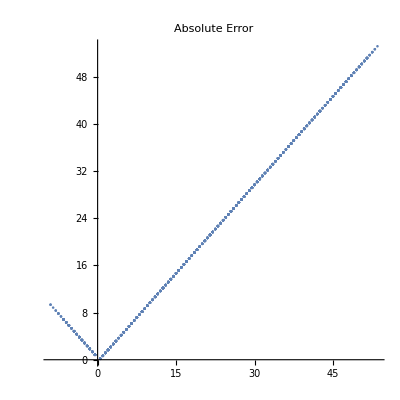

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

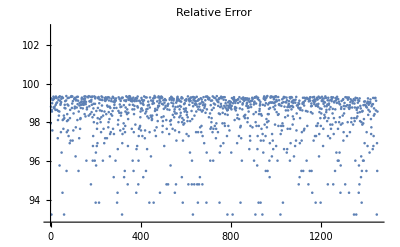

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

99.128

#### tallk5l5m5n5q50u60mfpos0, Net3, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

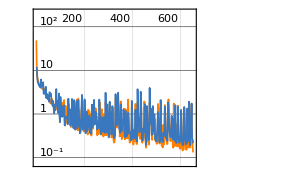
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:111663  rounds:653  time:3.6min  examples/s:32641
data | ,,  training examples:10942  validation examples:2189  processed examples:7146432  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:2.3×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{9.86665,17.6274,7.98797,7.64692,15.1241,6.66,5.55402,5.65965,4.58994,5.1546,4.79833,4.49643,4.58261,4.35167,4.99212,4.03064,4.23113,4.07299,3.58034,4.4772,7.64302,4.74232,5.66432,3.77124,3.54193,3.81572,4.66701,3.56109,5.65529,3.46204,7.23359,2.83879,2.97104,3.54381,3.39382,2.54058,3.38097,3.65048,2.92313,2.72466,4.37552,4.01972,2.35828,2.26245,2.62915,3.13588,2.58526,2.33649,2.36792,2.11522,2.05666,2.4987,2.83289,1.73918,2.12656,1.86816,4.44331,3.58264,2.5553,3.44695,1.07592,3.20887,3.27083,2.5329,1.76261,1.78285,2.36149,1.69218,1.06558,2.03695,2.30334,1.50266,1.06841,1.83985,1.06041,0.957281,1.11197,1.61621,1.59575,1.23225,1.21416,1.22047,2.19013,3.40587,4.05022,1.9004,1.77637,1.03929,0.932917,3.09428,1.31108,1.12414,1.25889,0.828579,1.84049,4.05008,0.953847,0.624081,1.20993,0.634751,0.664097,2.92975,1.98122,1.58281,1.03865,0.610321,2.48027,0.945476,0.762107,1.25183,0.721178,2.25231,0.959955,1.24942,0.810525,0.972323,2.07928,1.09836,0.580531,0.522291,0.482843,0.975711,0.957452,0.886012,0.649268,0.91806,0.804046,0.947768,0.66217,1.06583,0.684232,0.541513,0.628133,0.52818,0.604752,5.56394,1.30257,0.730521,0.4596,1.89555,0.715803,1.83525,0.555662,0.524011,0.443051,2.08005,1.29647,0.520006,0.570939,1.19648,3.23388,0.758377,0.402761,0.628189,0.433932,0.442811,0.504046,3.28673,0.896661,3.08983,1.54613,0.579085,0.418971,0.451871,0.387356,0.625473,0.748366,0.609304,2.7174,1.21816,0.599287,0.409319,0.414976,0.639212,0.517734,3.1153,1.05333,0.777452,1.52097,0.667072,0.753634,0.347398,0.376147,0.426168,0.349689,0.477706,0.434565,0.519512,0.809943,1.85235,1.65437,3.82299,0.785214,0.594577,0.505859,0.366206,0.560914,0.415979,0.367269,0.461593,0.652335,3.14352,1.17775,0.52077,0.547026,0.377596,0.349593,0.443593,0.799707,1.26511,1.68476,0.577981,0.509431,0.317127,0.407479,0.492778,0.904955,0.905851,0.507885,1.07253,0.91213,0.578236,1.30908,0.38553,0.347984,0.997074,0.620455,0.424832,0.320727,0.318993,0.37853,2.49194,0.772486,0.472277,0.625373,0.409366,0.769335,0.407976,0.380868,2.33328,2.59669,1.61802,0.626559,0.518543,0.764697,0.645062,0.460318,0.373504,1.87912,0.447109,1.46573,0.920364,0.552253,0.384922,0.493639,0.375759,0.909023,0.450171,0.426406,0.568321,0.350292,0.606788,0.884375,3.39028,1.78152,0.623395,0.62541,0.313358,0.284204,0.401849,0.273087,0.408869,1.39012,1.15485,0.545442,0.644313,0.362814,0.377574,0.399784,0.390905,0.523316,1.57861,0.398767,0.524038,0.371255,0.525959,0.345543,0.389153,3.95096,2.18257,0.60324,0.533221,0.355954,0.401429,0.280003,0.486165,4.20157,0.519573,0.329839,0.353034,1.02185,0.254099,0.328599,0.40757,2.86068,1.05544,2.76547,0.400381,0.351106,0.584773,1.72708,0.451442,0.321036,0.359763,0.245086,0.605388,0.337114,2.69273,1.63892,0.479155,0.399719,0.361455,0.295227,0.277638,0.281162,0.25935,0.403616,0.264369,0.368437,3.64419,2.05909,1.82681,1.09914,2.53082,0.749559,0.934227,0.616511,0.483716,0.831054,2.13524,1.81943,4.3266,1.53704,0.599457,0.754362,0.517176,0.395365,0.518125,0.35661,0.370713,0.36601,2.61145,0.707535,0.459798,0.33986,0.370845,0.562004,0.32827,0.282673,0.872907,0.322271,1.01182,0.419648,2.10558,1.76124,0.38533,0.303501,0.294364,0.287721,0.297971,0.294505,0.278441,2.06079,0.887575,0.618849,0.342163,0.270248,0.305301,0.355924,0.265251,0.269168,1.16435,1.06172,1.06213,0.912694,0.661425,0.280561,0.420657,0.272324,0.4594,0.296806,0.484517,0.335113,0.330316,0.429787,0.27237,0.221378,0.935281,3.05187,0.394536,0.627179,0.292455,0.271294,0.211614,0.323754,0.216102,0.322537,0.75181,0.241739,0.329072,0.234027,0.512879,1.92311,0.577122,0.270805,0.258776,0.258482,0.223133,0.443326,0.234386,0.235063,5.16496,2.23579,0.921572,1.06661,1.16843,0.407127,0.386033,0.373087,0.30772,0.28487,0.569646,0.314208,0.736215,0.268275,6.20453,1.89384,0.475646,0.297718,0.29388,0.285121,0.208036,0.200158,0.343232,0.257727,0.283369,0.646943,0.394963,0.365377,1.36058,1.36176,2.48327,0.91319,0.373268,0.258192,0.272598,0.193467,0.195796,0.309188,0.311674,0.587292,2.45939,0.581438,0.427093,0.365637,0.343239,0.23378,0.337728,0.191013,0.316695,0.204964,6.24671,1.67216,0.893042,0.696989,0.625228,0.575844,2.05314,0.566937,0.3669,0.361379,0.266748,0.294974,0.397166,0.486027,2.56058,0.959223,0.345499,0.484339,0.312464,0.252806,1.5075,1.19439,0.367905,0.36429,0.239162,0.281294,0.306164,0.34928,0.243771,0.223435,0.439907,0.237181,0.293361,0.284145,1.31944,1.8133,0.410242,0.628774,0.2611,0.29788,0.35522,0.234074,0.213931,1.00397,0.32507,2.82792,1.94273,1.50973,0.310164,0.401007,0.224482,0.27078,0.266097,0.221832,0.214499,0.239383,0.349276,0.507527,0.259706,0.23216,0.430847,0.379518,0.252982,0.219776,2.71506,1.02919,0.390119,0.346403,0.241701,0.314006,0.373521,0.212597,0.263952,0.257217,0.251349,0.233223,0.444484,3.24477,2.21252,1.03717,0.74447,0.469492,0.410327,0.427044,0.311425,0.329585,0.32282,0.304563,0.281479,0.400994,0.276642,0.36571,1.44897,0.589397,0.295466,0.310525,0.288457,0.239475,0.191061,0.330068,1.02362,0.537044,0.319135,0.317309,0.225236,0.259922,0.20479,0.196896,4.38401,0.289811,0.222775,0.215167,0.217569,0.340781,0.222199,0.260212,0.281139,0.568692,2.34502,0.612488,0.403703,0.230555,0.264715,0.180654,0.222655,0.219916,0.246204,0.32745,0.251461,0.242429,0.206782,2.6674,0.769343,0.870776,0.228596,0.207675,0.211197,0.202241,0.189634,0.201549,0.185514,0.338665,0.19446,0.206002,2.2716,1.87249,1.04618,0.264777,0.252879,0.305769,0.223028,0.182176,0.282202,0.249142,0.217012,0.209303,2.84162,0.745168,0.410424,0.246171,0.226821,0.299702,0.277365,0.273043,3.55864,1.32714,0.266944,0.211332,0.167739,0.201088,0.217056,0.601228,0.641,0.378775,2.7616,0.703706,0.370725,0.181481,0.316936,0.191294,0.195239,0.230249}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

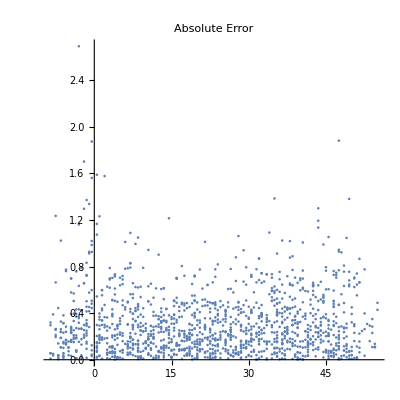

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

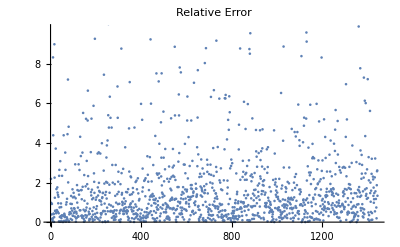

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.49423

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

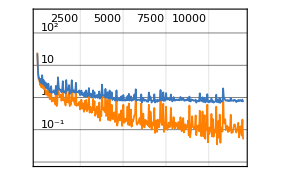
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:18min  examples/s:24379
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.4×10^-2
validation | ,,  loss:7.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

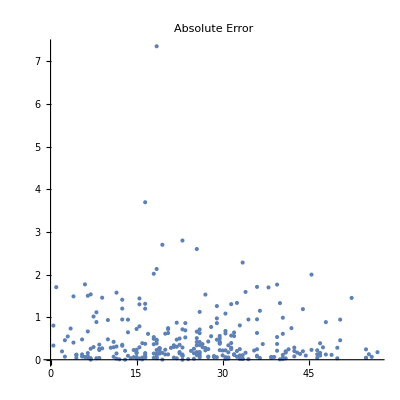

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

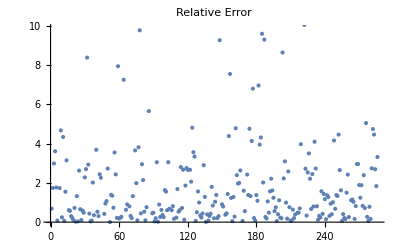

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.27794

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

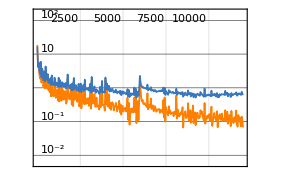
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:32min  examples/s:13805
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-2
validation | ,,  loss:5.57×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

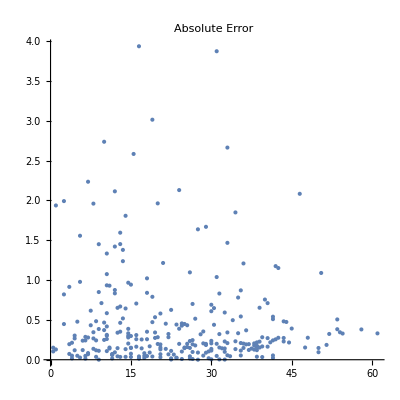

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

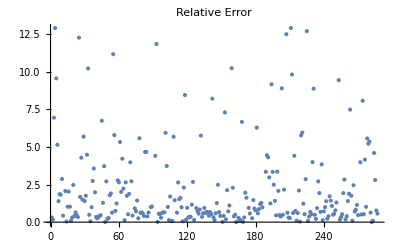

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.21632

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q30u50mfneg = ParallelTable[allprodgenneg[1, k, 2, l, 3,m, 4, n,30,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q30u50mfneg.mx", tallk2l2m2n2q30u50mfneg];
tallk2l2m2n2q20u30mfneg1 = ParallelTable[allprod1neg[1, k, 2, l, 3,m, 4, n,20,30], {k,-1,-3, -1},{l,-1,-3, -1}, {m,-1,-3, -1}, {n,-1,-3, -1}];
DumpSave["tallk2l2m2n2q20u30mfpos1.mx", tallk2l2m2n2q20u30mfpos1];*)
tallk2l2m2n2q40u50mfneg0 = ParallelTable[Quiet @ allprodθbyΔ[1, k, 2, l, 3,m, 4, n,40,50, 0], {k,0,-2, -1},{l,0,-2, -1}, {m,0,-2, -1}, {n,0,-2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg0.mx", tallk2l2m2n2q40u50mfneg0];
```

#### tallk2l2m2n2q40u50mfneg0, Net0, 39 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[331]]//N
```

{4.10134×10^-7,-8.20268×10^-7,3.14436×10^-6,-6.15091×10^-6,0.0000261318,0.00690038,2.55039,333.48,28578.7,1.27718×10^6,4.58949×10^7,1.04352×10^9,2.11083×10^10,3.02515×10^11,4.07557×10^12,4.18362×10^13,4.16687×10^14,3.32462×10^15,2.62228×10^16,1.71833×10^17,1.12555×10^18,6.29679×10^18,3.54451×10^19,1.74141×10^20,8.6409×10^20,3.80803×10^21,1.69832×10^22,6.82412×10^22,2.77733×10^23,1.03064×10^24,3.87445×10^24,1.34154×10^25,4.70427×10^25,1.53257×10^26,5.05364×10^26,1.55976×10^27,4.86918×10^27,1.43195×10^28,4.25593×10^28}→29.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

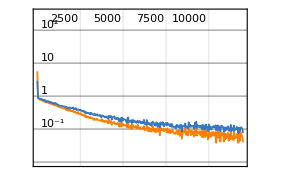
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:21min  examples/s:10224
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.4×10^-2
validation | ,,  loss:9.76×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

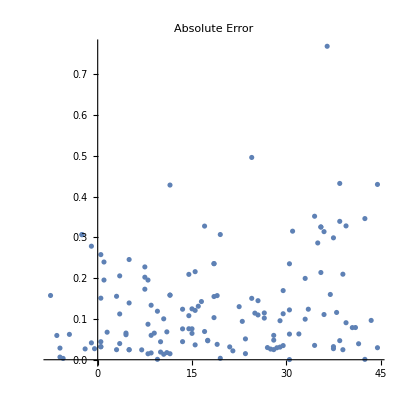

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

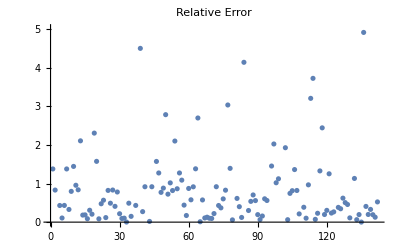

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.26061

#### tallk2l2m2n2q40u50mfneg0, Net3, 39 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

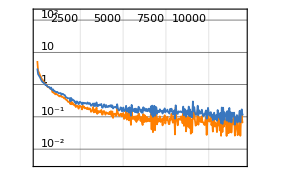
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:15min  examples/s:14259
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.81×10^-2
validation | ,,  loss:8.38×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

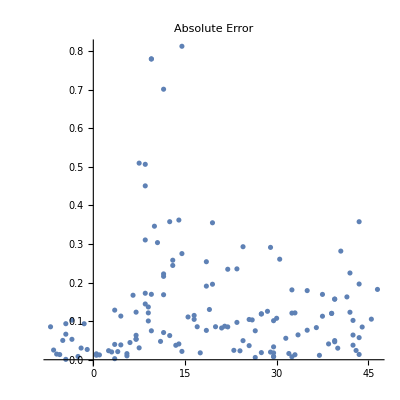

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

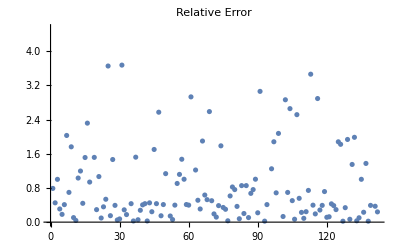

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.1453

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
plist=klmnneg[5, 400];
```

```mathematica
allprodgenbyΔneg[50,70,plist,plist[[61;;65]],0];
```

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
Length[data1]
```

922

```mathematica
Values[data1];
```

#### jacobibyΔ-klmn-neg, Net0, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

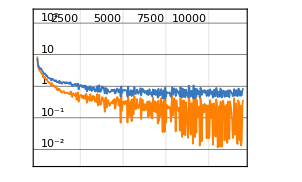
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.3min  examples/s:35752
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:5.28×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

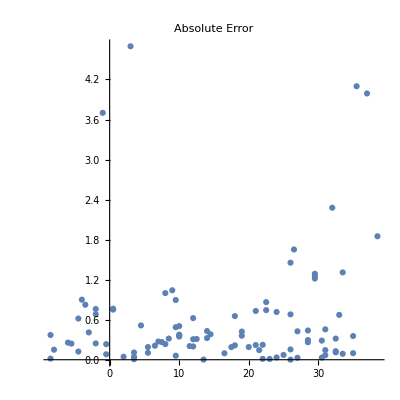

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

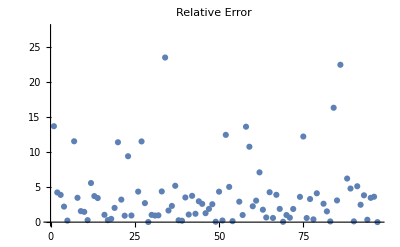

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

13.3438

#### jacobibyΔ-klmn-neg, Net3, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

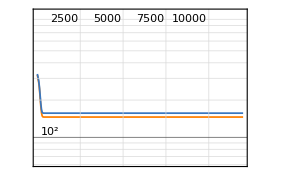
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.6min  examples/s:33129
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.46×10^2
validation | ,,  loss:1.57×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

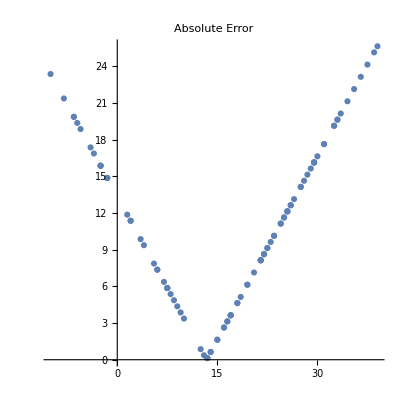

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

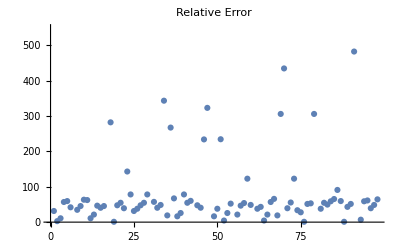

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

138.903

## 2 η^3 = θ_2θ_3θ_4

## Setting k = 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
k1 = ParallelTable[allprod1pos[1, 0, 2, l, 3,m, 4, n,70,80], {l, 3},{m,3}, {n, 3}];
```

```mathematica
<<tallk5l5m5n5q70u80mfpos1.mx; <<t2n50q30u70mfpos1.mx;
```

```mathematica
e1 = Flatten[tallk0l5m5n5q70u80mfpos1, 4];
(*e2 = Flatten[t2n70q60u100mfpos1, 1];
e3 = Flatten[t3n70q60u100mfpos1, 1];
e4 = Flatten[t4n70q60u100mfpos1, 1];*)
```

```mathematica
e1[[;;2]]
```

{{-1,27,-125,343,-729,1331,-2197,3375}→7/2,{1/12,-209/4,-96,5429/12,96,768,-32935/12,864,-1920,-1056,30819/4,288,-2400,6720,4416,-346523/12,9504,-384,-5760,-7200,-5376,548701/12,12000,-20160,-3936,19872,30432,-9408,-471109/4,31008,3168,10272,-25728,1920,-36288}→11/2}

```mathematica
Length /@ Keys[e1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
fdata1 = e1;
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
nk1 = If[Length[#]>= 59, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
(*nk2 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata2];
Length /@  nk2 // Union*)
```

{59,60,61,62,69,70}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
(*newkeys2 =nk2[[All,;;Min[Length /@ nk2]]];
newvalues2 = If[Length[Keys[#]]>= 26, Values[#], ##&[] ] & /@ fdata2;*)
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

3988

{59}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{3988}

3988

```mathematica
Length @ Keys[data[[1]]]
data[[1]]
```

59

{1/12,-41/6,-209/4,441/2,-223/6,192,-2545/12,-8509/6,-96,-2665/6,23317/6,377/2,-30631/12,42431/6,2400,-49277/6,-12449,3648,-6417/2,576,14691/4,2999/3,62965/6,-2304,50499/2,41239/6,8832,-7047/2,-195623/6,-104475/2,-164507/12,40793,14496,-14400,-492091/6,-14208,255173/3,324863/6,-43505/2,724307/6,-21888,-4416,971399/12,-584357/6,10272,-231579/2,-125743/3,54144,-240007/6,100951/6,-19488,-605789/3,7200,-93504,13824,210905,335297/4,475533/2,1522205/6}→6

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

2991

598

399

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 48 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:210251  rounds:4473  time:5.9min  examples/s:38282
data | ,,  training examples:2997  validation examples:599  processed examples:13456064  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 59 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:376000  rounds:8000  time:13min  examples/s:31393
data | ,,  training examples:2991  validation examples:598  processed examples:24064000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.26×10^-3
validation | ,,  loss:1.03×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.161518

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## u = 0

```mathematica
eta1pos[m_,  n_, nq_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[ EllipticTheta[2,0,q]^m EllipticTheta[3,0,q]^n EllipticTheta[4,0,q]^n,{q,0,nq}];
th2  = th1/q^(m/4);
cq = DeleteCases[CoefficientList[th2, q],0];
wt = m/2+2 n/2;
dt = cq -> wt;
Return[dt]]
```

```mathematica
th1  = Series[ EllipticTheta[2,0,q]^5 EllipticTheta[3,0,q]^5 EllipticTheta[4,0,q]^5,{q,0,10}]
```

32 q^(5/4)-480 q^(13/4)+2880 q^(21/4)-7840 q^(29/4)+3360 q^(37/4)+O[q]^(41/4)

```mathematica
eta1pos[5, 5, 10]
```

{{32,-480,2880,-7840,3360}→15/2}

```mathematica
etan500q200 = ParallelTable[eta1pos[n, n, 200],{n, 0, 500, 1/8}];
DumpSave["etan500q200.mx", etan500q200];
```

```mathematica
<<etan300q100.mx
```

```mathematica
etan100q50
```

```mathematica
e1 = Flatten[etan500q200, 3];
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{0,14,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
nk1 = If[Length[#]>= 70, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
newkeys1 =Simplify @ nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

2262

{70}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{2262}

2262

```mathematica
Length/@ Keys[data] // Union
```

{70}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 20000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.1min  examples/s:23336
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.09×10^-2
validation | ,,  loss:4.24×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:2.2min  examples/s:11670
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.49×10^-2
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.7min  examples/s:15094
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.79×10^-1
validation | ,,  loss:4.22×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.6min  examples/s:16311
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.11×10^-1
validation | ,,  loss:1.91×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.4min  examples/s:35160
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.7×10^-2
validation | ,,  loss:1.71×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:3.1min  examples/s:27529
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.71×10^-1
validation | ,,  loss:6.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.9min  examples/s:29141
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.96×10^-2
validation | ,,  loss:3.07×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.5min  examples/s:34530
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.18×10^-2
validation | ,,  loss:4.37×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* etan500q200 70 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:540000  rounds:20000  time:17min  examples/s:33878
data | ,,  training examples:1696  validation examples:339  processed examples:34560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.62×10^-2
validation | ,,  loss:5.35×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

## Individual θ_i without dividing by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
t1k40q50u60mfpos=ParallelTable[Quiet @ theta1[k,50,60],{k,40}];
DumpSave["t1k40q50u60mfpos.mx", t1k40q50u60mfpos];
t1k50q70u80mfpos=ParallelTable[theta1[k,70,80],{k,50}];
DumpSave["t1k50q70u80mfpos.mx", t1k50q70u80mfpos];
(*t1k80q120u150mfpos=ParallelTable[theta1[k,120,150],{k,80}];
DumpSave["t1k80q120u150mfpos.mx", t1k80q120u150mfpos];*)
```

#### t1k40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.8min  examples/s:26666
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.1×10^-1
validation | ,,  loss:1.39×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.366402

#### t1k40q50u60mfpos, Net3, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:6.2min  examples/s:20733
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-1
validation | ,,  loss:8.63×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.318925

#### t1k50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1360

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:7.9min  examples/s:25969
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.6×10^-2
validation | ,,  loss:4.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.257198

#### t1k50q70u80mfpos, Net3, 26 coeffs

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1360

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:12min  examples/s:17659
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.47×10^-2
validation | ,,  loss:5.5×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.342947

### θ_2

```mathematica
t2l40q50u60mfpos=ParallelTable[Quiet @ theta2[l,50,60],{l,40}];
DumpSave["t2l40q50u60mfpos.mx", t2l40q50u60mfpos];
t2l50q70u80mfpos=ParallelTable[theta2[l,70,80],{l,50}];
DumpSave["t2l50q70u80mfpos.mx", t2l50q70u80mfpos];
(*t2l80q120u150mfpos=ParallelTable[theta2[l,120,150],{l,80}];
DumpSave["t2l80q120u150mfpos.mx", t2l80q120u150mfpos];*)
```

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.1min  examples/s:26917
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.23×10^-2
validation | ,,  loss:1.1×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.775116

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.3min  examples/s:26274
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.27×10^-3
validation | ,,  loss:1.22×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.738755

#### t2l50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t2l50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t2l50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

2009

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:20min  examples/s:15231
data | ,,  training examples:1506  validation examples:302  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.78×10^-1
validation | ,,  loss:1.09×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.238111

### θ_3

```mathematica
t3m40q50u60mfpos=ParallelTable[Quiet @ theta3[m,50,60],{m,40}];
DumpSave["t3m40q50u60mfpos.mx", t3m40q50u60mfpos];
t3m50q70u80mfpos=ParallelTable[theta3[m,70,80],{m,50}];
DumpSave["t3m50q70u80mfpos.mx", t3m50q70u80mfpos];
(*t3m80q120u150mfpos=ParallelTable[theta3[m,120,150],{m,80}];
DumpSave["t3m80q120u150mfpos.mx", t3m80q120u150mfpos];*)
```

#### t3m40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.8min  examples/s:26546
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.24×10^2
validation | ,,  loss:3.42×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

68.4218

#### t3m40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:18003
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.53×10^-4
validation | ,,  loss:5.85×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.130769

#### t3m50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26632
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-2
validation | ,,  loss:7.65×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.04524

#### t3m50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:16min  examples/s:17959
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.38×10^-3
validation | ,,  loss:8.18×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0620383

### θ_4

```mathematica
t4n40q50u60mfpos=ParallelTable[Quiet @ theta4[n,50,60],{n,40}];
DumpSave["t4n40q50u60mfpos.mx", t4n40q50u60mfpos];
t4n50q70u80mfpos=ParallelTable[theta4[n,70,80],{n,50}];
DumpSave["t4n50q70u80mfpos.mx", t4n50q70u80mfpos];*)
(*t4n80q120u150mfpos=ParallelTable[theta4[n,120,150],{n,80}];
DumpSave["t4n80q120u150mfpos.mx", t4n80q120u150mfpos];*)
```

#### t4n40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.7min  examples/s:26664
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.33×10^2
validation | ,,  loss:3.52×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

49.7019

#### t4n40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:17967
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.47×10^-4
validation | ,,  loss:7.55×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.103263

#### t4n50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26354
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.71×10^-4
validation | ,,  loss:1.49×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0563935

#### t4n50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
```

```mathematica
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:14min  examples/s:21750
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.5×10^-3
validation | ,,  loss:1.59×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0445423

## Negative powers of θ_i

### θ_1

```mathematica
(*t1k40q50u60mfneg=ParallelTable[Quiet @ theta1[k,50,60],{k,-1, -40, -1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
t1k50q70u80mfneg=ParallelTable[Quiet @ theta1[k,70,80],{k,-1, -50, -1}];
DumpSave["t1k50q70u80mfneg.mx", t1k50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t1k40q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:7.0min  examples/s:36431
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.35×10^-3
validation | ,,  loss:8.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.54308

#### t1k40q50u60mfneg, Net3, 26 coeffs

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:9.6min  examples/s:26698
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:5.85×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.33966

### θ_2

```mathematica
(*t2l40q50u60mfneg=ParallelTable[Quiet @ theta2[l,50,60],{l,-1, -40, -1}];
DumpSave["t2l40q50u60mfneg.mx", t2l40q50u60mfneg];*)
t2l50q70u80mfneg=ParallelTable[Quiet @ theta2[l,70,80],{l,-1, -50, -1}];
DumpSave["t2l50q70u80mfneg.mx", t2l50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t2l40q50u60mfneg, Net0, 26 coeffs

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:5.4min  examples/s:35775
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.19×10^-1
validation | ,,  loss:1.04
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.93778

#### t2l40q50u60mfneg, Net3, 26 coeffs(r)

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:6.9min  examples/s:28011
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.59×10^-1
validation | ,,  loss:8.74×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.4772

### θ_3

```mathematica
t3m40q50u60mfneg=ParallelTable[Quiet @ theta3[m,50,60],{m,-1, -40, -1}];
DumpSave["t3m40q50u60mfneg.mx", t3m40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t3m40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:16978
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:3.91×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.542126

#### t3m40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16118
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.44×10^2
validation | ,,  loss:3.29×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

286.609

### θ_4

```mathematica
t4n40q50u60mfneg=ParallelTable[Quiet @ theta4[n,50,60],{n,-1, -40, -1}];
DumpSave["t4n40q50u60mfneg.mx", t4n40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t4n40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20422
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.47×10^-2
validation | ,,  loss:3.46×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.798023

#### t4n40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:8.7min  examples/s:21950
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.23×10^2
validation | ,,  loss:3.67×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

205.459

## Positive and negative powers together

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
```

### θ_1

```mathematica
t1k40q50u60mfAll=ParallelTable[Quiet @ theta1[k,50,60],{k,range40}];
DumpSave["t1k40q50u60mfAll.mx", t1k40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t1k40q50u60mfAll, Net0, 25 coeffs(r)

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:11min  examples/s:25944
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.71×10^-3
validation | ,,  loss:5.49×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

6.12769

#### t1k40q50u60mfAll, Net3, 25 coeffs

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:16min  examples/s:17936
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.47×10^-2
validation | ,,  loss:5.19×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

### θ_2

```mathematica
t2l40q50u60mfAll=ParallelTable[Quiet @ theta2[l,50,60],{l,range40}];
DumpSave["t2l40q50u60mfAll.mx", t2l40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t2l40q50u60mfAll, Net0, 22 coeffs(r)

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:13min  examples/s:26568
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-2
validation | ,,  loss:6.74×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.16186

#### t2l40q50u60mfAll, Net3, 22 coeffs

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:19min  examples/s:17974
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94×10^-1
validation | ,,  loss:3.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

### θ_3

```mathematica
t3m40q50u60mfAll=ParallelTable[Quiet @ theta3[m,50,60],{m,range40}];
DumpSave["t3m40q50u60mfAll.mx", t3m40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t3m40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:13min  examples/s:26677
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.43×10^2
validation | ,,  loss:4.59×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

#### t3m40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:20min  examples/s:18175
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.42×10^-2
validation | ,,  loss:7.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.306258

### θ_4

```mathematica
t4n40q50u60mfAll=ParallelTable[Quiet @ theta4[n,50,60],{n,range40}];
DumpSave["t4n40q50u60mfAll.mx", t4n40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t4n40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:18min  examples/s:19736
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.41×10^2
validation | ,,  loss:4.36×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

213.744

#### t4n40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2340

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:23min  examples/s:15332
data | ,,  training examples:1755  validation examples:351  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.99×10^-3
validation | ,,  loss:1.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.38193

## Individual θ_iwith division by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
tΔ1k40q50u60mfpos0=ParallelTable[theta1byΔ[k,50,60, 0],{k,40}];
DumpSave["tΔ1k40q50u60mfpos0.mx", tΔ1k40q50u60mfpos0];
tΔ1k50q70u80mfpos0=ParallelTable[theta1byΔ[k,70,80, 0],{k,50}];
DumpSave["tΔ1k50q70u80mfpos0.mx", tΔ1k50q70u80mfpos0];
(*tΔ1k70q90u100mfpos0=ParallelTable[theta1byΔ[k,90,100, 0],{k,70}];
DumpSave["tΔ1k70q90u100mfpos0.mx", tΔ1k70q90u100mfpos0];*)
```

#### tΔ1k40q50u60mfpos0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:8.6min  examples/s:14851
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:3.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.687776

#### tΔ1k40q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:13min  examples/s:9952
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.09×10^-3
validation | ,,  loss:3.81×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.585603

#### tΔ1k50q70u80mfpos0, Net0, 35 coeffs

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:18min  examples/s:11525
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.28×10^-3
validation | ,,  loss:4.67×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.468479

#### tΔ1k50q70u80mfpos0, Net3, 35 coeffs(r)

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:21min  examples/s:9808
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.63×10^-2
validation | ,,  loss:3.54×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.379703

### θ_2

```mathematica
tΔ2l40q50u60mfpos0=ParallelTable[theta2byΔ[l,50,60, 0],{l,40}];
DumpSave["tΔ2l40q50u60mfpos0.mx", tΔ2l40q50u60mfpos0];
tΔ2l50q70u80mfpos0=ParallelTable[theta2byΔ[l,70,80, 0],{l,50}];
DumpSave["tΔ2l50q70u80mfpos0.mx", tΔ2l50q70u80mfpos0];
(*tΔ2l70q90u100mfpos0=ParallelTable[theta2byΔ[l,90,100, 0],{l,70}];
DumpSave["tΔ2l70q90u100mfpos0.mx", tΔ2l70q90u100mfpos0];*)
```

#### tΔ2l40q50u60mfpos0, Net0, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11951
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.55×10^2
validation | ,,  loss:4.83×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

125.108

#### tΔ2l40q50u60mfpos0, Net3, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:19min  examples/s:10148
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:5.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.980556

#### tΔ2l50q70u80mfpos0, Net0, 36 coeffs

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 36];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:27min  examples/s:11980
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.57×10^-1
validation | ,,  loss:3.69×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.53233

#### tΔ2l50q70u80mfpos0, Net3, 36 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:31min  examples/s:10308
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.18×10^-2
validation | ,,  loss:6.39×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.886984

### θ_3

```mathematica
tΔ3m40q50u60mfpos0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,40}]; 
DumpSave["tΔ3m40q50u60mfpos0.mx", tΔ3m40q50u60mfpos0];
(*tΔ3m50q70u80mfpos0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,50}];
DumpSave["tΔ3m50q70u80mfpos0.mx", tΔ3m50q70u80mfpos0];*)
(*tΔ3m70q90u100mfpos0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{k,70}];
DumpSave["tΔ3m70q90u100mfpos0.mx", tΔ3m70q90u100mfpos0];*)
```

#### tΔ3m40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:10min  examples/s:18286
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.93×10^-3
validation | ,,  loss:5.79×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.286784

#### tΔ3m40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16272
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.2×10^-2
validation | ,,  loss:4.8×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.555659

### θ_4

```mathematica
tΔ4n40q50u60mfpos0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,40}];
DumpSave["tΔ4n40q50u60mfpos0.mx", tΔ4n40q50u60mfpos0];
(*tΔ4n50q70u80mfpos0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,50}];
DumpSave["tΔ4n50q70u80mfpos0.mx", tΔ4n50q70u80mfpos0];*)
(*tΔ4n70q90u100mfpos0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{k,70}];
DumpSave["tΔ4n70q90u100mfpos0.mx", tΔ4n70q90u100mfpos0];*)
```

#### tΔ4n40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17856
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-3
validation | ,,  loss:3.16×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.485268

#### tΔ4n40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17004
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.07×10^-2
validation | ,,  loss:1.1×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.602727

## Negative powers of θ_i

### θ_1

```mathematica
tΔ1k40q50u60mfneg0=ParallelTable[theta1byΔ[k,50,60, 0],{k,-1, -40, -1}];
DumpSave["tΔ1k40q50u60mfneg0.mx", tΔ1k40q50u60mfneg0];
(*tΔ1k50q70u80mfneg0=ParallelTable[theta1byΔ[k,70,80, 0],{k,-1, -50, -1}];
DumpSave["tΔ1k50q70u80mfneg0.mx", tΔ1k50q70u80mfneg0];*)
(*tΔ1k70q90u100mfneg0=ParallelTable[theta1byΔ[k,90,100, 0],{k,-1, -70, -1}];
DumpSave["tΔ1k70q90u100mfneg0.mx", tΔ1k70q90u100mfneg0];*)
```

```mathematica
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### tΔ1k40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:6.5min  examples/s:37186
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.71×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.180927

#### tΔ1k40q50u60mfneg0, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:11min  examples/s:21418
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.35×10^-2
validation | ,,  loss:1.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.174224

### θ_2

```mathematica
(*tΔ2l40q50u60mfneg0=ParallelTable[theta2byΔ[l,50,60, 0],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg0.mx", tΔ2l40q50u60mfneg0];*)
(*tΔ2l40q50u60mfneg1=ParallelTable[theta2byΔ[l,50,60, 1],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg1.mx", tΔ2l40q50u60mfneg1];*)
tΔ2l50q70u80mfneg0=ParallelTable[theta2byΔ[l,70,80, 0],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg0.mx", tΔ2l50q70u80mfneg0];
tΔ2l50q70u80mfneg1=ParallelTable[theta2byΔ[l,70,80, 1],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg1.mx", tΔ2l50q70u80mfneg1];
(*tΔ2l70q90u100mfneg0=ParallelTable[theta2byΔ[l,90,100, 0],{l,-1, -70, -1}];
DumpSave["tΔ2l70q90u100mfneg0.mx", tΔ2l70q90u100mfneg0];*)
```

#### tΔ2l40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20374
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.06×10^-2
validation | ,,  loss:2.36
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.32636

#### tΔ2l40q50u60mfneg0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:54min  examples/s:3538
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:2.92
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.00208

#### tΔ2l40q50u60mfneg1, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17404
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.03×10^-2
validation | ,,  loss:1.2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.24363

#### tΔ2l40q50u60mfneg1, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:12121
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94
validation | ,,  loss:3.71
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.43888

#### tΔ2l50q70u80mfneg0, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:18271
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.49
validation | ,,  loss:1.95
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.629451

#### tΔ2l50q70u80mfneg0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:17577
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.93×10^-1
validation | ,,  loss:3.13
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.727375

#### tΔ2l50q70u80mfneg1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:15min  examples/s:21298
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.05×10^-1
validation | ,,  loss:6.56×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.566101

#### tΔ2l50q70u80mfneg1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:17min  examples/s:18610
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:8.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.459067

### θ_3

```mathematica
tΔ3m40q50u60mfneg0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,-1, -40, -1}];
DumpSave["tΔ3m40q50u60mfneg0.mx", tΔ3m40q50u60mfneg0];
(*tΔ3m50q70u80mfneg0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,-1, -50, -1}];
DumpSave["tΔ3m50q70u80mfneg0.mx", tΔ3m50q70u80mfneg0];*)
(*tΔ3m70q90u100mfneg0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{m,-1, -70, -1}];
DumpSave["tΔ3m70q90u100mfneg0.mx", tΔ3m70q90u100mfneg0];*)
```

#### tΔ3m40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
Values[rawdata]
```

{-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,107/2,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,105/2,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,-45/2,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,-23,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,-47/2,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,-24,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13548
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.01×10^-3
validation | ,,  loss:7.03×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.662882

#### tΔ3m40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11714
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.39×10^-3
validation | ,,  loss:1.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.240945

### θ_4

```mathematica
tΔ4n40q50u60mfneg0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,-1, -40, -1}];
DumpSave["tΔ4n40q50u60mfneg0.mx", tΔ4n40q50u60mfneg0];
(*tΔ4n50q70u80mfneg0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,-1, -50, -1}];
DumpSave["tΔ4n50q70u80mfneg0.mx", tΔ4n50q70u80mfneg0];*)
(*tΔ4n70q90u100mfneg0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{n,-1, -70, -1}];
DumpSave["tΔ4n70q90u100mfneg0.mx", tΔ4n70q90u100mfneg0];*)
```

#### tΔ4n40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13392
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-2
validation | ,,  loss:1.16×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.405012

#### tΔ4n40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11805
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.56×10^-3
validation | ,,  loss:2.93×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.493767

## Positive and negative powers together

### θ_1

```mathematica
(*tΔ1k40q50u60mfAll=ParallelTable[theta1byΔ[k,50,60, 0],{k,range40}];
DumpSave["tΔ1k40q50u60mfAll.mx", tΔ1k40q50u60mfAll];*)
(*tΔ1k50q70u80mfAll=ParallelTable[theta1byΔ[k,70,80, 0],{k,range50}];
DumpSave["tΔ1k50q70u80mfAll.mx", tΔ1k50q70u80mfAll];*)
```

```mathematica
tΔ1q70u0mf200q0 = ParallelTable[theta1byΔu0[k, 70, 0], {k,range200}];
DumpSave["tΔ1q70u0mf200q0.mx", tΔ1q70u0mf200q0];
```

#### tΔ1k40q50u60mfAll, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:27min  examples/s:13428
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:1.72×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.347008

#### tΔ1k40q50u60mfAll, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
Export["tΔ1k40q50u60mfAll_net3.wlnet",tNet]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:22min  examples/s:16198
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.07×10^-2
validation | ,,  loss:1.86×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

tΔ1k40q50u60mfAll_net3.wlnet

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.359283

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

### θ_2

```mathematica
tΔ2l40q50u60mfAll0=ParallelTable[theta2byΔ[l,50,60, 0],{l,range40}];
DumpSave["tΔ2l40q50u60mfAll0.mx", tΔ2l40q50u60mfAll];
tΔ2l50q70u80mfAll0=ParallelTable[theta2byΔ[l,70,80, 0],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll0.mx", tΔ2l50q70u80mfAll0];
tΔ2l50q70u80mfAll1=ParallelTable[theta2byΔ[l,70,80, 1],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll1.mx", tΔ2l50q70u80mfAll1];
```

```mathematica
(*tΔ2q30u0mf40q0 = ParallelTable[theta2byΔu0[l, 30, 0], {l,range40}];
DumpSave["tΔ2q30u0mf40q0.mx", tΔ2q30u0mf40q0];*)
tΔ2q50u0mf100q0 = ParallelTable[theta2byΔu0[l, 50, 0], {l,range100}];
DumpSave["tΔ2q50u0mf100q0.mx", tΔ2q50u0mf100q0];
(*tΔ2q70u0mf200q0 = ParallelTable[theta2byΔu0[l, 70, 0], {l,range200}];
DumpSave["tΔ2q70u0mf200q0.mx", tΔ2q70u0mf200q0];*)
```

#### tΔ2l40q50u60mfAll0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:26min  examples/s:14854
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:9.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.75374

#### tΔ2l40q50u60mfAll0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:30min  examples/s:13002
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.18×10^-2
validation | ,,  loss:1.29
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.70932

#### tΔ2l50q70u80mfAll0, Net0, 35 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:41min  examples/s:15119
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-1
validation | ,,  loss:4.03×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.82778

#### tΔ2l50q70u80mfAll0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:48min  examples/s:13070
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.04
validation | ,,  loss:1.81
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.78524

#### tΔ2l50q70u80mfAll1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:35min  examples/s:17751
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.01×10^-1
validation | ,,  loss:4.35×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.42044

#### tΔ2l50q70u80mfAll1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ2q50u0mf100q0, Net0, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.6min  examples/s:23926
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.46×10^-4
validation | ,,  loss:1.69×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0676657

#### tΔ2q50u0mf100q0, Net3, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:24948
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.63×10^-4
validation | ,,  loss:6.56×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

17.635

### θ_3

```mathematica
tΔ3m40q50u60mfAll=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,range40}];
DumpSave["tΔ3m40q50u60mfAll.mx", tΔ3m40q50u60mfAll];
(*tΔ3m50q70u80mfAll=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,range50}];
DumpSave["tΔ3m50q70u80mfAll.mx", tΔ3m50q70u80mfAll];*)
```

```mathematica
(*tΔ3q30u0mf40q0 = ParallelTable[theta3byΔu0[m, 30, 0], {m,range40}];
DumpSave["tΔ3q30u0mf40q0.mx", tΔ3q30u0mf40q0];*)
tΔ3q50u0mf100q0 = ParallelTable[Quiet @ theta3byΔu0[m, 50, 0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
(*tΔ3q70u0mf200q0 = ParallelTable[theta3byΔu0[m, 70, 0], {m,range200}];
DumpSave["tΔ3q70u0mf200q0.mx", tΔ3q70u0mf200q0];*)
```

```mathematica
allprodθbyΔu0[1,0, 2, 0, 3, 1, 4, 0, 50,0]
```

CoefficientList::poly: 2+1/q$4048335+12 q$4048335+24 q$4048335^2+92 q$4048335^3+180 q$4048335^4+544 q$4048335^5+1040 q$4048335^6+2715 q$4048335^7+5072 q$4048335^8+11948 q$4048335^9+21840 q$4048335^10+47684 q$4048335^11+85408 q$4048335^12+«24»+37102218528 q$4048335^37+56364953136 q$4048335^38+86725611764 q$4048335^39+130718632800 q$4048335^40+199182448896 q$4048335^41+297989634592 q$4048335^42+449976736548 q$4048335^43+668443861856 q$4048335^44+1000908975584 q$4048335^45+1476883540704 q$4048335^46+2194081585165 q$4048335^47+3216782471840 q$4048335^48+«2» is not a polynomial.

{}

```mathematica
uΔ0q[t3_,m_,t4_, n_, nq_, qInPower_] := Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + m/2 + n/2-6(-qInPower);
dt = Thread[cq2->wt];
(*If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];*)
Return[dt]]
```

```mathematica
uΔ0q[3,2,4,5,20,1]
```

{{1,-6,-8,112,-60,-908,1152,4128,-7195,-11340,23784,19328,-41148,-23448,17280,30976,66888,-18386,-120856,-144960}→19/2}

```mathematica
th1  =Assuming[q>0,Series[EllipticTheta[2,0,q]^0 EllipticTheta[3,0,q]^2 EllipticTheta[4,0,q]^5,{q,0,17}]]
```

1-6 q+4 q^2+40 q^3-66 q^4-104 q^5+232 q^6+192 q^7-396 q^8-494 q^9+552 q^10+1080 q^11-1000 q^12-1320 q^13+1552 q^14+1344 q^15-1986 q^16-2512 q^17+O[q]^18

```mathematica
Series[EllipticTheta[3,0,q]^1 EllipticTheta[4,0,q]^0,{q,0,7}]
```

1+2 q+2 q^4+O[q]^8

```mathematica
CoefficientList[th1,u]
```

{1+2 q+2 q^4}

```mathematica
DeleteCases[CoefficientList[th1,u],0]
```

{1+2 q+2 q^4}

```mathematica
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-(1))),{q,0,7}]]&/@(DeleteCases[CoefficientList[th1,u],0])
```

{q-6 q^2-8 q^3+112 q^4-60 q^5-908 q^6+1152 q^7+O[q]^(85/12)}

```mathematica
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq
```

{{1,-6,-32,256,384}}

```mathematica
tΔ3q50u0mf100q0 = ParallelTable[uΔ0q[3,m,4,0,50,0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
```

#### tΔ3m40q50u60mfAll, Net0, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:27min  examples/s:13987
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.73×10^-2
validation | ,,  loss:2.17×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.80189

#### tΔ3m40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:31min  examples/s:12024
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.18×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.413791

#### tΔ3q50u0mf100q0, Net0, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25430
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.06
validation | ,,  loss:2.09
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.60356

#### tΔ3q50u0mf100q0, Net3, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25768
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^-2
validation | ,,  loss:6.65×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.473795

### θ_4

```mathematica
tΔ4n40q50u60mfAll=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,range40}];
DumpSave["tΔ4n40q50u60mfAll.mx", tΔ4n40q50u60mfAll];
(*tΔ4n50q70u80mfAll=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,range50}];
DumpSave["tΔ4n50q70u80mfAll.mx", tΔ4n50q70u80mfAll];*)
```

```mathematica
(*tΔ4q30u0mf40q0 = ParallelTable[theta4byΔu0[n, 30, 0], {n,range40}];
DumpSave["tΔ4q30u0mf40q0.mx", tΔ4q30u0mf40q0];*)
tΔ4q50u0mf200q0 = ParallelTable[theta4byΔu0[n, 50, 0], {n,range200}];
DumpSave["tΔ4q50u0mf200q0.mx", tΔ4q50u0mf200q0];
(*tΔ4q70u0mf200q0 = ParallelTable[theta4byΔu0[n, 70, 0], {n,range200}];
DumpSave["tΔ4q70u0mf200q0.mx", tΔ4q70u0mf200q0];*)
```

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:26min  examples/s:14244
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.56×10^-2
validation | ,,  loss:1.13×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.482538

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:25min  examples/s:15122
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.29×10^2
validation | ,,  loss:4.4×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

258.785

```mathematica
Series[Δ2[]]
```

## CHL models

```mathematica
process[list_]:=Log[N[Abs[list]]]/.Indeterminate->0
```

```mathematica
net1=NetChain[{256, Ramp,256,Ramp,128, Ramp, 128,Ramp, 64, Ramp, 32, Ramp, 8, Ramp, 1},"Input"->30, "Output"->1]; 
net2=NetChain[{512, Ramp,256,Ramp,256, Ramp, 128,Ramp, 128, Ramp, 64, Ramp, 32, Ramp, 1},"Input"->30, "Output"->1];
```

```mathematica
TrainAndTest[data_,net_,method_,epochs_]:=Module[{trainset,valset,testset,trainedNet,testvals,testpreds,abserrors,relerrors},
{trainset,valset,testset}=datapartition[data];
trainedNet=NetTrain[net,trainset,All,ValidationSet->valset,MaxTrainingRounds->epochs,Method->method]["TrainedNet"];
testvals=Flatten[testset[[;;,2]]];
testpreds=Flatten[trainedNet/@testset[[;;,1]]];
abserrors=Abs[testvals-testpreds];
relerrors=abserrors/testvals*100;
Return[{testvals,testpreds,abserrors,relerrors,Mean[relerrors]}]
]
```

```mathematica
processResults[{testvals_,testpreds_,abserrors_,relerrors_,_}]:={ListPlot[Transpose[{testvals,Abs[testvals-testpreds]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1,ImageSize->Medium],ListPlot[relerrors,PlotLabel->"Relative Error",PlotRange->All,ImageSize->Medium],"mean relative error = "<>ToString@Mean[relerrors]}
```

## Data generation

```mathematica
SetDirectory[NotebookDirectory[]<>"data2"];
```

```mathematica
k[n_]:=24/(n+1)-2;
```

```mathematica
f[n_,q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^(k[n]+2)DedekindEta[n/(2π ⅈ)Log[q]]^(k[n]+2)
```

```mathematica
coeffnum=29;
maxpower=1000;
```

```mathematica
coeffGenPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[Series[f[n,q]^pow,{q,0,coeffnum+pow}],q][[pow+1;;]],{pow,maxpower}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenPositive[n],{n,{1,2,3,5,7}}];
```

```mathematica
coeffGenNegative[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,coeffnum+pow}],q],{pow,-1,-maxpower,-1}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenNegative[n],{n,{1,2,3,5,7}}];
```

```mathematica
filenamePos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"]
```

```mathematica
filenameNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"]
```

```mathematica
randPositive=Rationalize[SetPrecision[RandomReal[{0.01,1000},2000],4], .01]
randNegative=Rationalize[SetPrecision[RandomReal[{-1000,-.01},2000],4], .01]
```

{2000/29,2503/3,771,34/7,2311/5,1067/3,1883/2,875,1731/2,1311/2,8843/22,1661/8,2680/3,1310/3,871,29/4,1423/3,9957/19,1789/8,3997/6,1509/8,1909/4,914/11,874,9179/51,5381/18,8486/9,7756/11,1781/4,2057/3,1198/9,2579/3,561,225,480,955/7,287/10,701,1028/7,2925/7,645/17,1107/2,36/7,987,7031/8,641,1595/6,1346/3,1462/3,1813/2,2071/4,163/10,2029/3,2321/5,1119/5,970/9,3793/7,1247/3,2095/3,194/3,1226/5,712,3925/4,2293/3,2466/7,5593/6,1706/5,2260/9,665/4,3848/27,2680/3,809/17,2203/3,1345/7,4491/10,5711/8,595/2,1324/5,1305/4,1826/3,983/5,1352/3,1837/2,919,9907/13,683/14,3259/6,1249/3,2442/5,2441/6,997/7,1901/2,2743/3,2043/10,4594/5,955/4,675/2,512,1589/2,3341/10,4406/39,298,1979/11,2227/4,6239/12,2501/3,85/6,500,1757/2,2519/3,1601/4,2294/11,2047/7,2965/3,7811/28,271/16,971/2,6698/7,1967/2,6166/9,1999/3,426,4481/5,1207/2,5167/19,1633/3,1252/7,1037/2,934/3,1403/12,3437/4,1698/5,1841/3,2999/3,1023/2,6097/8,263/12,4780/7,4180/13,1030/7,1801/3,1167/4,2870/3,6031/16,81/11,3469/4,4106/5,7454/21,2702/5,643/2,4021/6,599/3,2413/3,1631/3,1927/2,3623/4,1169/2,5605/6,1753/8,2464/3,885/4,991,3965/6,1083/4,2255/4,2395/3,2525/6,991/7,1837/2,4389/5,881/9,2179/8,4144/5,793/3,1859/3,436/15,7223/28,1129/7,3133/5,1831/3,151/6,5224/25,2501/11,3751/8,1921/10,694/19,986,5491/6,3633/8,1249/4,1318/5,1832/3,1353/2,288,789/7,598,1655/3,1710/13,1429/5,2412/7,2505/4,4954/5,1160/7,1399/4,1121/2,1889/4,449/30,1724/3,2072/3,2911/8,4964/5,1293/4,1984/5,2305/3,2491/3,554,763/6,2266/3,477,35/2,1032/5,3214/9,1813/2,3525/11,1711/19,1439/4,1352/3,3482/5,1231/8,1945/2,2539/3,942,2679/5,8846/9,1393/2,721,7541/10,281/11,2821/3,811/2,1643/4,1969/8,2932/3,847/3,2998/5,2420/3,2453/3,1873/5,413/6,3689/6,2383/10,1714/3,2005/3,4029/5,1217/2,1319/3,2887/13,3472/13,2561/6,1297/3,1522/7,3753/4,971/2,2055/4,6988/17,1043/4,695,1427/2,7039/11,883/4,987,1579/3,3471/4,981,2663/3,673/9,1401/8,1633/3,1147/2,217/3,709/3,1927/4,1784/5,3383/8,409/5,212/25,1541/2,1369/4,1901/2,5697/22,1392/5,890/3,8159/60,1467/2,1695/8,2122/3,1751/4,533/5,607/5,2288/3,1725/4,1901/2,4393/36,846,834/5,3456/5,3884/11,448,1328/5,3795/4,37/5,8603/17,4691/6,2446/3,903,8185/44,2650/3,1951/2,3924/5,2919/13,1337/5,1415/2,1117/3,801/2,5137/7,106/9,1943/8,3019/9,2182/9,861,1301/3,1969/2,2578/3,5795/7,474,943/3,442,700,3241/4,1477/4,2223/8,1967/2,2492/9,4247/12,948,1487/3,1736/3,719,2059/3,307/8,1978/3,820,1611/4,937,187/5,2858/3,1519/3,2613/5,1420/3,4169/6,1889/2,7649/9,1985/2,4149/5,340/7,1502/13,1109/2,758,2069/9,2997/4,1335/4,351/2,1443/2,4474/5,912/11,641/3,2479/3,1849/2,502/5,1276/51,5565/23,1377/5,2277/7,1255/3,2945/3,2773/12,6488/9,134/9,6025/12,483/5,793/2,721,3548/13,1889/4,7/11,1995/16,1477/4,2699/3,2932/3,743/8,1291/4,1382/3,634/5,1824/5,2822/19,783/4,1270/11,497/4,1410/19,1773/4,1004/3,9153/11,698,2254/3,3473/4,1103/3,2852/5,1472/19,997/2,623/13,1503/14,158,4927/16,3653/7,2551/3,1973/2,308,1915/2,441,1526/3,1789/3,954,3278/15,2591/16,2702/3,806/3,1481/2,2263/10,433,572/3,1324/3,1357/4,77/9,2767/3,4717/18,1057/3,1049/2,2902/3,3199/39,3063/7,753,2495/6,3683/5,1851/2,759/2,2505/4,2588/5,903/5,1234/3,1007/8,1857/19,174/17,513,2941/5,3411/5,1841/4,470/3,3664/11,4061/7,1295/6,3121/4,4481/9,1328/3,292/3,929,958,2968/3,966,1775/3,899/4,1997/2,581,1201/2,657/10,476/13,2263/4,2020/11,1561/8,2836/3,1609/3,997/8,747,1348/5,1171/5,7019/9,519/2,671/8,2837/3,485,97/10,3879/4,171/11,949,3991/4,1406/5,794/7,91/4,4229/5,1222/3,1267/4,1042/5,7451/10,1869/2,645,495/26,2998/11,5821/10,1843/3,258,2174/3,1578/7,3648/7,1696/17,4324/5,951,3734/5,1685/2,1868/3,769/4,1169/2,5431/6,1237/4,1773/2,920,1271/2,6103/7,1601/2,2521/3,1682/3,8328/11,2512/3,1923/2,1735/2,1623/5,2812/3,3843/4,989/9,2990/3,1421/9,3579/4,2926/3,1838/3,749/4,3299/6,1413/2,1609/7,9670/11,1115/2,692/3,5441/8,1237/2,2407/5,843/2,3016/7,923,1721/4,1201/4,2047/15,2212/3,1259/7,4519/5,3734/11,2569/8,559/7,4176/5,1853/3,978,6022/9,4781/6,585/2,481,859/2,2559/8,2309/3,1762/3,1775/4,1751/2,466,1688/3,3135/16,923,5069/28,7521/8,1339/3,1803/2,859,1203/2,1221/10,630,1376/3,1829/2,2125/3,2170/9,1597/2,2404/3,1161/2,821/3,913,568,1407/5,286,1789/3,2627/4,1043/2,2246/3,4714/5,877/7,1151/2,2364/5,1989/7,2038/3,1521/17,722,1537/5,1617/2,849/4,450,2455/4,895,2002/3,2500/3,1311/5,4246/5,1588/3,2782/5,867/2,2723/9,769/4,4201/5,1705/2,5849/17,1943/2,721/38,1781/4,3851/6,2867/6,904,1438/5,117/7,4789/14,2197/9,2428/3,2126/3,1644/5,1603/4,1838/3,1041/5,2705/4,1969/5,1066/3,1225/4,557/9,546,1901/4,3156/7,523/7,645,1279/7,663/2,1996/3,329/5,1813/2,5791/16,2281/5,5185/6,184,838,1646/9,1305/4,2111/6,2962/3,3611/5,8241/20,997/3,1001/2,2063/3,1538/3,481/9,1325/2,1811/4,1381/14,1504/3,2399/6,1054/7,1201/2,1685/3,2608/3,2821/3,1671/2,1612/3,141/8,2386/3,904/3,4334/7,1217/6,2260/3,1979/2,1437/2,966/11,571/12,2420/3,1985/2,1973/2,905/2,679/12,3166/5,1157/3,2387/3,313,6631/8,508/3,815/3,3574/11,2345/17,1861/3,882,3295/4,1396/3,1664/21,645,1693/2,1897/2,3783/8,1675/4,2866/3,705/8,866,455/8,2156/3,1596/11,868/9,99/7,2813/3,3629/4,3759/10,2054/3,2600/7,1943/2,8659/13,2335/3,1571/2,3571/5,3057/4,3169/6,519/7,1208/9,1134/5,974/3,231/10,1112/5,6782/7,1390/3,9017/14,522,1472/3,1941/2,1469/5,1183/2,17/12,4537/21,493,3275/4,357,2219/3,1907/4,4229/10,841/3,4215/8,536/7,6149/10,1074/19,3835/4,1577/5,6737/8,619/3,2786/5,2813/15,412/7,1711/6,1243/4,1615/3,1125/4,5107/23,69/11,1739/2,1749/7,2353/3,1778/3,2483/3,104/7,884,2837/6,4634/5,2483/3,5320/9,715,1209/11,2404/3,818,4294/5,2991/4,1563/2,1011/4,5953/6,5197/6,2342/7,2783/3,1417/4,1703/6,1078/3,2017/12,2011/15,1664/3,2201/3,740,2467/3,9395/14,1178/3,908/3,499/25,807/5,2452/3,766/3,1375/2,1333/2,6585/8,911/5,3807/4,15/4,707/4,1674/5,1208/13,880,907/6,2215/3,2075/3,3195/4,3042/11,775,7071/17,1895/4,5788/7,1054/5,2033/7,4757/6,1381/2,969/2,941/6,586,1041/7,1669/2,2739/26,2944/3,1817/2,1405/2,3839/5,2726/3,785/6,3504/13,973/2,1215/2,2461/3,1117/2,2374/5,3343/16,2391/4,2492/3,2379/5,2230/3,917/4,1077/5,3835/27,219/7,402/7,1502/19,2305/9,4209/5,8099/12,1917/5,1549/2,1615/4,401,171,905,1863/4,675,2239/4,1529/6,878/3,5/4,3637/4,1801/15,2191/6,2107/3,2147/6,1195/4,967,3431/10,1251/2,951/8,6980/7,321,3173/6,894/7,1613/13,331/2,9541/30,2572/3,1274/5,1299/2,2051/4,3012/5,5907/7,1631/3,1360/3,5165/9,2276/7,1849/2,1547/5,421,971,499/2,794/3,1942/3,2090/3,2593/3,2260/3,740,1207/2,4205/6,269/8,1147/4,1210/3,1861/2,1259/5,1367/2,368/5,3961/10,1361/2,2053/4,3165/7,1908/13,1852/3,1149/8,633,249,1789/2,5781/14,977,3665/4,1285/2,658,1717/2,1243/2,391/2,6173/7,3413/5,1845/4,211/10,3217/7,123,1887/2,777/10,5633/11,874/3,1612/5,23/4,771,2026/3,1521/5,2668/3,1357/6,3145/4,2089/3,3619/4,715/6,797,2351/4,2285/7,1915/3,81/4,1517/4,2237/3,1847/3,1677/4,724/5,2120/3,2395/6,4041/5,17/5,235/3,6682/41,2990/3,947/2,4573/9,2425/3,7391/8,2069/6,2195/3,481/5,763,3223/4,2540/3,2297/3,1213/2,217,384,1222/3,488,378,3425/6,2251/3,2654/3,1507/3,1282/3,743/2,986/5,506,1533/5,678,1901/2,573/2,907/3,1511/3,6777/7,673/5,2362/3,3999/4,459/2,2218/3,2734/3,3055/4,1853/4,1793/4,661,6377/8,64,946,819,1474/3,1419/4,829,1756/3,919/3,664/13,1189/13,2251/3,804,2018/3,61/12,841,949,842/3,3121/8,3785/4,8773/12,567,2986/3,1693/3,1982/5,655/6,795/4,3545/6,2205/4,1135/2,917/2,1521/5,2241/4,1121/6,2066/3,1301/3,3834/5,466,1852/3,7709/15,2942/5,807/13,1417/2,1381/19,1537/2,2037/4,2073/8,5110/19,3844/7,1606/3,2947/6,1556/5,1721/7,1244/3,827/2,99/10,901/6,1996/3,2360/3,1521/7,964,4616/9,922,2899/3,2845/3,2170/3,1447/2,389/5,911/6,1690/3,1967/3,2072/3,225/8,1985/2,2017/3,7553/8,3469/6,3051/5,675/2,3231/4,1574/7,2374/3,1291/41,1589/2,1881/7,2143/3,3449/6,2949/4,3443/4,2277/4,1861/2,1376/3,571/9,1297/10,1559/2,3098/5,2447/3,1685/9,527,644/11,5345/6,919/2,6040/11,4641/20,1504/3,2378/3,5867/14,2181/5,3465/4,4190/7,775/4,959/6,1139/8,1951/2,3941/9,1925/8,1979/4,2003/11,2585/3,1823/4,1571/5,1093/3,2698/3,1283/9,1169/19,1747/2,2975/11,1400/3,1743/2,5452/7,2752/3,1259/2,2248/3,993,5464/9,802/3,744,1190/3,1433/2,3605/4,1843/2,1631/3,69/10,809,1861/3,1682/3,3889/6,475/7,7183/8,7889/8,432,803/8,602/3,479/8,1580/3,4331/5,471,987/5,1421/2,2229/4,2131/9,413/4,6029/9,938,2837/4,2539/5,2729/3,1510/7,5363/7,1849/3,2013/5,1389/2,443,3519/5,349/4,1705/7,1952/5,1562/3,1925/9,958/5,2998/3,7631/72,526,1216/7,2006/3,2933/4,3255/11,1462/7,1169/2,2155/3,1745/2,845/8,741,925/3,3222/5,7719/8,2206/3,3081/4,2063/4,1141/2,2821/3,5389/12,374/3,3649/4,4483/27,3552/5,1143/2,2709/5,3383/6,2266/3,1637/7,3641/5,1879/3,1801/2,633/26,2429/3,455/3,1457/2,2699/3,2558/3,2479/6,2951/3,1757/2,2756/3,1234/5,608/11,2452/3,677/6,989/26,1465/3,2768/3,200/7,665/3,2444/5,789/4,1641/17,2818/5,459/5,2692/13,1323/4,833/10,3951/4,669,2839/3,1557/2,1334/5,812/13,3269/38,771/22,1809/4,9598/21,1407/5,2234/3,4867/6,730,148/3,1917/10,4912/17,2584/3,1361/2,1593/2,1086/7,1833/2,1606/3,704/7,943/5,322/5,1681/2,2827/5,1807/2,1786/3,2766/5,1874/3,2039/3,1798/7,515,689,733,484/3,5083/7,693/8,2929/3,4937/8,593,200/11,281,1758/7,2275/4,724/11,1881/2,2348/3,1395/2,1222/3,6770/7,2534/3,2375/4,311,2992/3,6140/7,1999/2,3569/5,1339/2,908/5,207/2,989/3,2533/3,1489/5,849,203/12,2528/3,5628/13,803/3,1258/11,1573/4,685/2,2909/10,3959/4,2026/3,138/19,929,833,846/5,1321/2,6404/7,733/3,1335/2,1993/3,1383/2,991/4,889/23,1457/3,1180/7,2457/4,1955/2,2455/3,933/2,1189/3,2342/3,1811/3,1027/5,35/13,1356/7,2438/9,2200/3,2873/4,8373/13,1957/4,109,1912/5,3521/5,1253/2,1325/3,2032/3,2693/3,987/2,556,1259/5,1603/3,1501/7,911/3,680/7,517,2975/3,697/2,2141/3,5849/8,955/4,3869/4,6215/8,4251/5,2267/3,449/2,1505/3,4996/5,2240/3,548/7,1623/2,2961/4,2729/10,4479/5,1277/3,531,2141/8,8018/11,1975/2,1535/2,409/8,1455/2,1909/2,1463/3,7615/8,957/4,1294/3,1500/17,1279/17,1321/11,1109/12,3785/11,2839/6,1325/3,1046/3,1165/2,1412/3,1824/5,32/31,3038/5,827/5,2827/13,1527/2,3723/11,846,207/5,396,2855/4,594,1084/5,5487/13,686/5,2710/3,2225/8,1513/5,1069/2,257/14,7676/9,2657/5,2416/3,1349/8,8424/25,2881/4,331,1102/3,5473/7,2081/4,416/17,1899/2,1354/9,881/2,1451/3,1551/4,2447/3,4886/5,1759/2,941/2,2935/3,1397/5,883,421,834,786,4865/16,2903/3,893/11,2558/3,1875/2,2543/6,2596/3,3431/4,4261/6,839/6,1738/3,2278/3,386/5,1037/4,1481/6,1213/4,1850/3,2065/3,7541/10,1771/2,626/3,4939/10,1819/3,1207/4,2829/4,8988/11,3614/9,754,2174/3,3193/6,2611/5,1859/3,2446/5,2408/3,831,913/3,1013/4,2742/5,1285/3,4019/9,5246/11,1849/2,434,2167/6,1417/6,1477/2,3488/9,665,7913/8,4159/8,2215/4,811/4,5457/11,1571/3,2079/5,2918/3,521,1285/8,1057/8,868,3649/12,1337/3,5399/6,1954/3,887/4,503/5,5858/9,4969/8,2798/3,1609/2,569/11,1123/6,2021/3,2137/4,503/2,1243/3,39,4983/8,889/3,2090/3,87/7,1387/2,4469/5,2671/5,2548/3,860/13,974/25,2164/3,3019/5,3121/5,1221/2,1327/6,1271/18,1453/3,3677/6,858,1656/5,1835/16,1073/10,1291/3,31/7,1148/5,3573/4,2659/7,2254/5,2469/4,1869/2,1297/4,959/3,3467/4,2800/9,1187/5,1629/2,1274/3,1793/2,3457/7,712/23,983/4,1543/9,599/7,797,2353/4,2060/3,1257/2,3865/4,707,1077/8,3644/5,1696/3,1508/3,1453/3,1817/4,1337/3,2087/6,1334/7,2096/3,575/2,683,4599/11,2162/7,3551/12,1589/3,1342/3,734,1745/2,2860/3,2061/8,729/2,433/3,1963/3,2389/6,778/3,958/3,3794/11,1817/3,458/7,800/9,2505/4,3951/52,1461/2,5161/6,1100/3,1632/7,1114/7,2423/3,2572/3,9101/28,4127/12,707/2,2674/5,780,2751/5,1271/10,1853/5,313/5,1653/2,4250/7,2899/7,7521/8,2524/7,3956/5,893/5,3537/4,2057/5,1366/5,948,2273/11,3577/24,1072/3,994,8396/9,2869/3,5001/20,499/2,7667/9,1109/5,973,159/7,186/11,1417/2,3119/4,4642/21,2791/5,572,1730/3,6209/9,1465/3,623/9,2437/3,6257/8,2654/5,1417/6,2800/3,1720/3,1462/9,1871/4,6821/18,2120/3,964/3,2566/7,573/2,6022/27,2446/3,2222/7,1061/2,2375/4,809,1753/4,1827/2,1609/3,3244/5,2783/4,1993/3,2203/5,1909/4,520,3592/7,3028/7,1571/2,1672/3,1712/3,533/9,1351/3,1769/3,4687/6,2420/3,1103/3,3161/5,2551/9,1637/3,1023/4,4607/8,3847/6,2822/3,1737/2,3227/4,539/30,1965/2,1378/7,304,1078/5,330,8383/11,2195/3,2792/3,1663/9,132/5,1379/3,2284/3,2717/10,635/3,2665/3,493,2501/4,5963/7,705,991/2,2311/3,289/11,5419/10,347/14,4432/7,7787/17,1655/2,745/2,14/5,1799/6,2307/4,4810/17,303,82/5,1779/2,1015/2,1851/37,3506/19,889/9,1402/3,1081/4,4314/5,743/8,2138/3,1029/5,414/7,633/2,2978/9,3764/5,766/5,1286/11,2365/3,747,2315/7,607,1481/4,3029/15,681/5,1257/5,1731/4,2890/3,2803/5,5097/8,3936/5,2855/3,1653/2,1018/5,3124/5,2138/3,1618/9,1989/2,1367/2,1605/4,369/7,2408/3,2165/3,2713/3,733/4,843/2,1723/2,881/2,971/9,4489/12,116/3,2862/5,2551/3,2794/5,71/12,2591/4,2002/3,1444/3,2599/3,2597/4,1961/3,1760/3,2281/3,1174/3,1361/4,183/4,2182/5,4390/11,1453/3,2759/3,225,1947/2,277/9,557/4,97,3477/22,2696/5,2677/3,768/13,1267/2,1574/3,1907/2,2440/7,1599/2,1611/4,3621/10,6047/24,393/5,4247/18,2216/5,318,916,923,849/4,910,593/3,3212/7,1691/2,3669/10,301/8,6739/10,2915/3,4817/16,3169/5,1953/2,1025/4,644,3884/5,977/2,2941/3,9181/12,531/4,2141/4,1127/5,1065/2,1967/19,277,2989/4,2839/5,867,2563/3,991,1612/3,508/3,963,1447/5,867/4,337/2,373,747/7,2927/8,752/9,2882/3,277,770/3,355,1851/2,1451/2,1831/5,818/9,1361/4,1505/2,1427/4,3135/4,3279/7,2925/7,2827/6,1516/9,989/15,416/11,1204/3,6546/7,4689/5,485/7,1199/2,647/2,2479/4,1855/2,4166/5,2081/13,4706/9,1873/2,947,2210/3,5424/7,2668/3,1872/7,2533/3,2674/5,1092/5,1685/2,3571/5,393/4,4527/8,503/2,2322/11,65/4,4264/7,2002/3,9921/20,528,1328/3,453/2,2057/4,2653/5,1589/5,531/2,1825/6,877/39,1577/10,871/8,2894/5,4811/5,106/13,686,6175/18,1081/21,1443/4,2231/3,2509/4,2544/7,959,1639/5,1207/5,584/5,2931/4,7668/11,2915/3,511/12,1841/4,361,7529/10,1553/4,679,755/28,3297/8}

{-242/13,-1221/2,-2368/3,-831,-1210/3,-1090/7,-1999/10,-2095/6,-4357/6,-3263/5,-1802/3,-4746/5,-641/7,-820,-632,-2507/11,-624,-612,-6119/10,-1237/3,-2391/5,-1347/4,-2199/4,-700,-706,-1515/2,-1727/5,-185/7,-1505/19,-3802/13,-1882/3,-1411/7,-2659/5,-1870/3,-1449/8,-4296/11,-2299/9,-1395/4,-1393/16,-604/3,-4756/5,-1611/4,-1095/2,-1469/6,-1631/2,-1273/6,-1819/4,-3119/5,-1593/2,-1307/3,-776,-329/6,-2471/5,-838/5,-2318/3,-1525/2,-49/5,-1229/5,-3681/5,-405/2,-1957/2,-1047/8,-824,-345/8,-7237/9,-2641/3,-1703/4,-965,-1919/7,-2500/3,-2579/20,-842,-1447/3,-403,-1437/2,-1571/7,-4603/6,-8527/14,-1485/2,-2239/3,-1609/3,-8807/17,-2704/3,-1307/4,-1919/2,-2246/7,-1021/2,-32,-1519/2,-4474/7,-511/8,-2717/5,-2819/3,-1481/2,-2725/3,-1717/2,-3307/9,-1011/2,-1954/3,-180/11,-453,-2061/5,-9049/29,-773/5,-6796/7,-7439/8,-698,-8281/15,-2121/4,-2698/7,-2335/3,-1823/4,-1384/3,-1897/2,-2024/5,-683/19,-790,-6935/8,-5095/6,-3929/4,-1173/2,-3589/4,-17/4,-872/5,-87/25,-1510/3,-671/13,-3066/5,-1127/19,-1643/3,-1088/5,-92/9,-629/3,-2141/4,-739/6,-7732/37,-6236/7,-2351/4,-6889/10,-941,-852/7,-2953/3,-2560/3,-1095/4,-7757/28,-388,-6915/7,-6527/17,-4849/5,-2223/29,-1921/3,-1551/2,-2009/3,-1155/2,-1695/2,-1161/2,-7217/9,-1555/6,-3859/6,-4656/5,-787/7,-977/3,-3986/5,-1268/3,-3621/4,-1937/5,-5297/6,-331/12,-757/2,-3965/4,-1863/2,-2801/4,-1779/2,-470/3,-1523/4,-2548/3,-1952/5,-1933/3,-3879/4,-1612/3,-3592/7,-1394/3,-2005/3,-3409/8,-2471/6,-7121/8,-19/5,-2448/5,-32/5,-301/8,-6652/9,-469,-1531/17,-6875/7,-527/6,-5027/7,-1033/5,-1252/3,-4327/8,-807,-6931/7,-2314/5,-1443/2,-667,-651,-2842/3,-1143/2,-1137/2,-3431/26,-9857/16,-706/3,-1627/5,-637,-833/3,-1775/12,-1173/2,-941/7,-1041/5,-2410/3,-1415/2,-688,-851/5,-3434/5,-663/5,-989/3,-2687/10,-754,-1798/5,-2593/5,-1165/3,-2425/7,-911,-2825/3,-1749/14,-2469/5,-639/2,-1009/4,-1949/4,-3937/4,-3506/7,-681,-2165/3,-401/9,-1873/2,-583/8,-2140/3,-1979/22,-1523/7,-7910/11,-1988/5,-3719/4,-3658/7,-9450/11,-1967/3,-1166/3,-217/13,-1996/3,-919/6,-2507/3,-2294/3,-1895/2,-4377/8,-4003/7,-1984/7,-2291/3,-1509/4,-826,-1913/6,-134/11,-953,-1851/2,-892,-1468/5,-4668/7,-1591/3,-2599/4,-5143/6,-885/7,-313/12,-3649/4,-1866/5,-733/4,-1187/2,-777,-2126/5,-1495/3,-1698/5,-340/7,-4169/5,-788,-1108/19,-1478/3,-1268/3,-898/3,-1736/3,-227/20,-3619/4,-401/2,-2050/3,-2981/3,-953/4,-1496/3,-739/7,-1971/2,-1865/4,-1585/3,-194,-916,-1891/5,-3979/5,-1397/3,-3347/6,-5336/9,-1772/5,-1976/5,-1521/4,-2725/3,-133/9,-1534/3,-5489/7,-1691/17,-60,-9055/18,-2053/6,-1427/3,-738,-1009/4,-1554/17,-1531/6,-1673/2,-531,-1496/3,-4195/6,-179,-1447/4,-1061/2,-1661/3,-2428/3,-893/3,-2489/3,-3279/4,-1081/6,-571/6,-1432/3,-3998/7,-5395/6,-1381/2,-1611/7,-1046/5,-341,-3945/4,-1294/7,-3893/9,-3575/4,-2213/3,-1373/2,-3446/13,-973/9,-964,-2415/4,-1261/5,-3657/62,-327/2,-1282/5,-729,-1629/4,-1691/3,-2414/3,-2397/11,-6041/8,-990,-409/12,-2663/9,-693,-834,-866/13,-1942/3,-1759/8,-87/14,-4121/6,-2438/3,-3161/5,-1949/2,-825,-3893/4,-59/8,-788,-1861/2,-2163/4,-9519/80,-8436/13,-318/5,-927,-2654/7,-768,-1955/2,-1079/7,-2047/3,-829,-1801/8,-1929/4,-882,-3549/4,-2470/3,-4454/5,-1018/3,-1967/3,-108/19,-1253/4,-1183/4,-1153/2,-820/23,-4067/6,-4244/5,-1323/2,-3673/4,-2201/3,-914/5,-746/5,-1128/17,-146/7,-2357/6,-2475/4,-1947/4,-2565/4,-4759/8,-1099/3,-1683/4,-2057/3,-599/2,-2419/3,-1280/3,-4014/5,-598/7,-4563/7,-2008/3,-1183/2,-1767/2,-3589/4,-1519/2,-998,-1282/3,-1423/3,-5291/9,-1561/12,-719/4,-5519/8,-1285/2,-4510/9,-985,-1084/3,-7140/11,-989/3,-2380/3,-1819/8,-3524/5,-2502/7,-1346/5,-2345/4,-1269/5,-3569/5,-1917/2,-5109/10,-2556/35,-1487/2,-4161/13,-799/6,-3837/4,-1941/4,-2117/3,-1463/3,-885,-328,-936,-3632/7,-3879/5,-2803/3,-547/3,-947/3,-898,-2681/6,-1921/2,-1198/3,-1023/16,-4301/5,-2554/3,-1314/5,-4789/6,-6509/7,-1677/2,-901/2,-3144/17,-5930/11,-1015/2,-995/3,-1169/3,-1499/2,-660,-2030/3,-1494/5,-4364/5,-1597/8,-2685/17,-1178/5,-275/12,-823/4,-881/3,-816,-5647/16,-6799/66,-1717/3,-514/5,-1347/4,-631/2,-1583/4,-954/5,-1599/64,-2119/5,-2353/3,-2714/5,-474,-428/9,-487,-669/2,-2030/3,-3985/4,-545/4,-1545/2,-4671/5,-2743/3,-2704/3,-2536/7,-589/4,-3869/10,-3759/8,-2942/3,-367/5,-1375/3,-1407/2,-2663/3,-1079/2,-3593/5,-7876/35,-9421/15,-609,-1249/3,-2828/3,-2365/3,-1322/13,-439/20,-2369/4,-1027/9,-4535/7,-802,-1783/4,-904,-825/2,-2737/3,-3921/5,-2523/4,-1293/4,-639,-910,-1937/2,-1303/3,-2727/5,-22/5,-923/5,-295/6,-4879/10,-2781/4,-1709/2,-376/11,-2843/3,-1079/5,-1883/2,-1893/5,-3193/7,-2362/5,-980,-1143/2,-1405/2,-4009/6,-1275/11,-627/2,-1188/23,-1834/3,-161,-1261/22,-1270/3,-1486/15,-1339/3,-6329/10,-1195/2,-1243/4,-1289/3,-2717/3,-2185/4,-647/2,-2505/8,-855/2,-519/2,-2401/15,-5891/62,-1453/2,-2213/3,-9461/10,-2867/6,-4598/7,-4049/23,-999/2,-4454/11,-1996/7,-1099/3,-679/8,-637/4,-703/4,-839/17,-699,-7249/48,-1717/3,-1646/7,-1777/2,-1325/4,-917,-1565/2,-3043/6,-1217/4,-6672/7,-621,-6447/13,-2533/3,-2871/8,-1917/2,-1599/4,-3947/4,-1967/2,-8559/10,-1899/2,-1616/3,-1909/5,-409/6,-3116/5,-934,-1989/2,-8416/9,-1943/2,-2121/10,-893,-819/2,-3749/10,-1873/4,-747/2,-2015/4,-1967/2,-2454/5,-1905/2,-1079/7,-1115/2,-695/3,-629/21,-444,-2381/3,-610/9,-6964/11,-1258/3,-4131/7,-1903/3,-1147/2,-2162/3,-1963/3,-1091/10,-4217/8,-2980/3,-1912/3,-534/7,-2758/3,-2239/4,-540,-795/2,-3479/4,-3455/6,-193/7,-386/3,-2060/3,-631/2,-1996/3,-1599/4,-6131/7,-918,-4685/6,-3991/6,-1492/7,-2879/5,-442,-2808/7,-2873/3,-2473/4,-2323/3,-1945/2,-1689/2,-2055/7,-1161/2,-2184/5,-1382/3,-1783/2,-2113/3,-152,-1429/3,-2594/3,-1847/2,-956/3,-4275/17,-317/6,-1775/2,-762/7,-626/3,-7079/12,-2013/4,-1891/9,-1679/3,-1113/4,-1205/4,-2244/7,-2217/4,-4045/6,-782,-801/2,-6571/10,-1990/3,-694/7,-632,-1705/2,-1867/2,-617/9,-4879/6,-3206/5,-1883/4,-4166/17,-1411/2,-387/2,-827/2,-1522/3,-3293/6,-1277/7,-7797/14,-1372/3,-2281/6,-1589/3,-407/6,-4124/5,-1223/3,-432,-1491/5,-7501/11,-757/4,-2840/3,-468,-992/3,-699,-198/5,-4717/9,-1301/13,-251/7,-2413/4,-2494/3,-1198/5,-2683/9,-4259/15,-2299/3,-3754/9,-1779/8,-7567/43,-1607/2,-1252/5,-2343/4,-1202/3,-634/13,-2658/11,-4665/8,-638/5,-5167/7,-4967/9,-4699/9,-6115/11,-2185/3,-321,-1124/9,-3868/5,-1893/2,-1817/3,-2029/6,-888/5,-769/2,-947/2,-3887/6,-903/2,-1546/3,-1079/3,-1661/9,-756/5,-2606/3,-209/5,-1143/7,-898,-376/9,-1797/5,-1778/5,-4321/6,-1655/9,-3662/7,-1851/2,-2425/4,-1607/5,-729/4,-1867/2,-911/4,-3319/7,-726/5,-1223/4,-1923/2,-2269/3,-1355/8,-805/8,-3289/4,-277/8,-3533/5,-2870/3,-6810/7,-2737/4,-1288/5,-4164/5,-1109/3,-2335/3,-2266/3,-2061/4,-5609/8,-1341/4,-1223/2,-1553/4,-1002/5,-965/3,-801,-1919/3,-2243/4,-1149/2,-591/4,-923/4,-1199/2,-2927/3,-4096/9,-1745/2,-1595/4,-2181/5,-3939/4,-2659/4,-713/2,-4036/7,-3546/5,-3154/5,-2084/3,-1543/3,-250/7,-1470/17,-2903/4,-663,-2528/3,-222,-1965/4,-274/5,-2848/3,-944,-2572/3,-510,-2747/10,-841,-915/4,-647,-3971/4,-2098/3,-1519/8,-49/8,-593/2,-6349/10,-1509/2,-983,-3461/4,-1847/3,-2567/3,-1330/3,-636,-539/10,-6599/10,-3529/12,-2709/4,-1725/8,-1051/2,-2333/5,-2697/4,-1534/3,-3077/9,-6043/19,-1002/11,-1493/4,-3304/5,-3131/9,-947/7,-1969/41,-2188/3,-1129/10,-327/7,-1511/4,-525/8,-6566/11,-535/2,-2802/5,-1959/2,-2234/3,-601/15,-535,-2483/6,-1693/3,-1443/5,-351/10,-939/2,-2389/5,-1052/3,-2492/3,-1237/5,-823,-1683/5,-593/2,-484/7,-165/4,-2039/5,-1481/6,-6345/13,-1480/3,-1052/3,-1056/5,-2089/3,-4843/7,-2335/4,-2341/7,-1023/2,-1857/2,-2039/4,-2669/3,-2415/4,-410,-734/3,-3019/4,-2213/3,-4093/6,-1679/2,-2924/3,-4237/12,-1981/2,-161,-2610/17,-1330/13,-5678/7,-750/7,-4169/6,-3695/4,-880/7,-9489/16,-897/2,-4476/5,-332/3,-1081/3,-981,-4391/9,-1611/4,-2419/6,-1645/8,-2165/3,-282/7,-407/12,-1210/3,-323/2,-2371/3,-1591/9,-1521/5,-4681/10,-6946/15,-2336/3,-2623/3,-455/4,-958,-1742/3,-466,-914/3,-3217/4,-705,-3821/4,-1685/4,-3279/8,-2092/3,-815/2,-1637/3,-1365/2,-3769/4,-1423/3,-380,-491/3,-3491/6,-1388/9,-2444/7,-2338/3,-7151/8,-970,-3674/7,-1871/3,-1573/6,-1531/5,-2957/3,-1707/5,-1651/5,-1429/2,-2619/5,-1487/3,-6206/17,-1657/2,-4503/8,-389/2,-5363/6,-2848/7,-1657/2,-1743/2,-1184/7,-1999/2,-3883/4,-4379/30,-1029/10,-4561/8,-5975/8,-1279/2,-135/2,-3579/5,-535/22,-985,-2167/4,-1352/9,-2539/3,-919/5,-711/5,-524,-3578/9,-685/9,-407/3,-4948/7,-2300/3,-839/6,-2785/6,-1331/2,-3947/4,-1784/3,-911/2,-1238/5,-2506/3,-562/3,-3309/4,-444,-1557/2,-1455/2,-5053/14,-1073/2,-2039/9,-1355/14,-156/11,-1753/4,-1408/13,-207/7,-1195/3,-1172/5,-861/4,-3591/8,-1559/4,-695/2,-1609/5,-1435/2,-5921/14,-218,-535/7,-1759/6,-133/10,-1881/2,-1721/3,-2639/33,-543/5,-2077/3,-797,-3522/7,-896,-1837/2,-977,-1630/3,-329/4,-1413/2,-2353/12,-3485/4,-1885/2,-4634/5,-977/2,-301/9,-567/2,-1453/3,-1301/5,-1929/2,-2176/5,-2864/3,-154/5,-985/4,-383,-1053/2,-4304/21,-3134/5,-955/8,-2949/17,-203/4,-570,-1931/10,-523/2,-7209/14,-1307/3,-2636/3,-1509/2,-1733/3,-1713/4,-2170/3,-1438/3,-1677/2,-936,-8929/9,-1089/2,-1043/8,-1913/3,-3925/6,-2185/6,-2672/3,-856/3,-87,-815/2,-709/5,-3589/4,-3385/6,-467/12,-2605/3,-709/3,-1375/9,-3839/6,-3561/13,-898/39,-273,-757/6,-452/3,-2711/4,-902/13,-667/3,-298/5,-2547/5,-1283/7,-2552/3,-5381/18,-3991/5,-1039/2,-1667/4,-1307/3,-1510/3,-1743/8,-385/2,-3464/11,-4506/5,-1518/37,-2275/3,-457/8,-2125/4,-937,-2314/3,-1663/6,-1143/7,-388,-3499/7,-704,-1965/2,-1591/4,-3268/5,-630,-6513/16,-2584/3,-4213/6,-3929/6,-7211/10,-1949/2,-571/4,-2677/3,-8979/20,-439/3,-2017/5,-649,-2009/22,-8047/9,-2804/9,-859/4,-2899/18,-943/9,-765,-1921/3,-7219/10,-2811/4,-2892/7,-1278/5,-1773/2,-961,-1823/2,-1665/2,-2318/3,-1851/2,-2569/3,-4986/5,-620/3,-40,-3893/4,-1338/5,-865/32,-1839/4,-295,-1387/11,-339,-4490/9,-2143/3,-2447/10,-661/2,-3084/5,-4572/7,-116/13,-579/7,-1792/3,-736,-1705/2,-1873/2,-1777/3,-1249/2,-1448/5,-778/5,-1502/3,-2828/5,-1339/2,-3679/4,-1163/5,-2771/4,-838,-766,-4311/8,-2217/5,-2300/3,-1939/3,-2252/3,-1373/15,-1093/6,-1641/4,-1294/3,-754/9,-3821/5,-1977/2,-2251/4,-1091/9,-2332/3,-131/7,-386/5,-2105/22,-867/2,-4429/5,-1401/4,-219/4,-1321/2,-1636/3,-1827/5,-816,-1849/2,-507/10,-3113/6,-1673/3,-1215/2,-5185/6,-2920/7,-1958/3,-1189/2,-471,-7536/11,-701/4,-1511/4,-1391/14,-124/3,-1632/5,-1849/3,-257/6,-832/5,-886/3,-1411/2,-2995/3,-569/4,-641,-282/5,-1455/8,-1822/3,-8000/9,-1617/2,-2407/3,-5633/44,-6999/10,-4577/6,-1803/2,-1831/3,-1671/2,-704/3,-972,-7435/9,-2930/3,-1634/5,-605/8,-3439/8,-461,-2337/8,-2623/3,-470,-352,-5329/6,-1213/20,-2009/4,-414/5,-1889/3,-1241/3,-2821/3,-921,-2251/6,-2705/3,-148/5,-1003/12,-681/5,-1108/3,-3079/4,-743/3,-409/9,-1359/5,-1292/3,-5801/8,-1403/3,-2678/3,-1831/15,-568/5,-1525/12,-1835/3,-3407/4,-8139/37,-7943/12,-365/7,-1384/5,-4185/14,-1993/2,-8794/9,-814,-2786/3,-7583/8,-783/2,-2435/7,-3866/5,-794,-1549/2,-3922/5,-2547/5,-6579/11,-3763/4,-2134/7,-2380/13,-805/6,-1401/4,-3137/5,-3371/4,-837,-756,-1987/7,-2887/3,-841,-9141/20,-169/10,-3392/5,-2791/9,-1182/5,-1689/4,-1527/2,-2855/3,-922,-1199/2,-1079/5,-2672/3,-2195/3,-1267/2,-4529/10,-923/6,-5372/9,-3335/13,-1941/4,-3076/17,-1660/3,-1093/14,-1421/2,-309/7,-1828/5,-967/2,-1343/2,-447,-1663/2,-609/5,-4717/6,-1417/2,-1153/3,-2617/4,-3343/6,-4134/5,-2161/6,-499/6,-1895/4,-250,-2101/6,-5564/7,-5447/8,-900,-1891/2,-1895/3,-119/2,-1089/10,-2187/4,-936,-271/8,-243,-5459/7,-1961/6,-1435/3,-6707/7,-1910/3,-998/3,-1441/5,-1332/7,-1761/4,-86/3,-2929/6,-5773/6,-5067/7,-701/6,-2152/3,-2673/16,-3745/4,-1299/2,-180,-1309/3,-4119/5,-3532/7,-1145/3,-477/2,-3327/4,-2556/7,-1958/3,-2810/3,-3259/4,-834/5,-4507/6,-1801/8,-2205/4,-1873/2,-2438/3,-994,-981,-263/7,-1131/5,-1157/2,-2743/7,-3177/4,-2879/3,-1366/3,-2479/3,-2815/6,-3568/5,-8323/19,-952/3,-1151/9,-690,-1336/3,-1725/2,-6767/16,-3773/6,-460/13,-281/2,-1187/2,-1183/3,-4045/9,-2697/10,-7199/18,-1976/3,-1217/2,-681/10,-866,-13/27,-1427/6,-297,-5485/6,-1285/2,-3867/4,-519/5,-2659/3,-984/5,-1561/2,-636/7,-1431/2,-659/5,-1013/8,-1369/24,-4040/7,-5853/7,-545/4,-1611/4,-2296/5,-2689/3,-1523/2,-699/13,-1835/3,-4441/6,-2803/3,-8303/12,-4959/5,-691,-3753/7,-326/3,-724,-6764/15,-1608/5,-4629/5,-2564/3,-1043/23,-1061/3,-1087/3,-1700/7,-3821/7,-1256/15,-2387/3,-1909/2,-1439/2,-458/3,-2042/3,-2961/10,-61/4,-1989/4,-2881/3,-1625/6,-1275/2,-1525/3,-349/2,-5551/6,-3371/10,-1792/9,-4152/7,-1627/2,-1543/2,-4717/7,-1810/3,-3599/8,-818/5,-3671/4,-3114/7,-2810/3,-7789/11,-3701/5,-1241/3,-913,-1380/7,-878,-1457/3,-4447/6,-288/25,-2563/5,-2954/5,-3266/5,-511/2,-1491/8,-645/4,-1478/3,-2039/4,-126/29,-890,-487,-1703/5,-203/10,-659/9,-3628/39,-803/6,-2477/7,-1997/4,-2121/4,-781/3,-2764/3,-1231/3,-2758/3,-2195/3,-3079/5,-1670/3,-1229/2,-1511/4,-1555/3,-2423/3,-445/12,-139/9,-1163/2,-1619/2,-6839/26,-1451/4,-1021/4,-1412/5,-2275/6,-1601/2,-64/3,-8074/9,-5387/6,-1079/3,-2765/4,-1355/2,-938/9,-3023/6,-2921/3,-2609/5,-8497/9,-1801/2,-4721/5,-7991/8,-1297/4,-233/5,-2852/9,-2875/3,-5747/6,-8867/13,-336/5,-1897/8,-9071/27,-541,-1569/5,-2965/3,-755/3,-383/3,-4195/6,-1945/3,-8229/11,-170/13,-1729/10,-3917/4,-2374/3,-2327/3,-1969/2,-1977/2,-2167/3,-1199/16,-1938/5,-4774/5,-919,-713/9,-354,-1859/2,-1391/3,-1411/2,-7183/19,-9249/16,-783/5,-474,-1054/3,-837,-2884/5,-941/4,-2139/5,-3821/7,-196/5,-950,-1431/10,-2256/5,-455,-2090/3,-1983/5,-687/4,-1085/2,-945,-2609/3,-1033/3,-613/2,-430/3,-1913/5,-1090/7,-1978/3,-5994/11,-795/2,-669/2,-2363/4,-830/3,-882,-936/7,-5897/6,-675/2,-1421/2,-1008/5,-1457/4,-6017/8,-616/3,-1909/2,-2376/5,-91/9,-337/9,-5734/7,-4201/50,-903,-1237/12,-1971/2,-2221/3,-905/6,-92/9,-2244/5,-1453/6,-1499/5,-1659/4,-1024/21,-3935/4,-2224/3,-1573/3,-1683/2,-5249/8,-3761/6,-2249/3,-1324/3,-1057/12,-475/4,-934/5,-6497/9,-2414/5,-213/4,-975/4,-3531/5,-1761/2,-2626/5,-1021/5,-692/7,-62/9,-884,-2105/3,-513/7,-2314/3,-2801/3,-1014/5,-277/13,-1379/6,-1661/3,-1089/5,-2564/3,-3953/6,-496,-7625/8,-2311/3,-1684/9,-992/3,-6302/11,-819,-1433/3,-3338/11,-2300/3,-5409/10,-1152/7,-304/5,-1013/4,-3282/5,-1361/7,-1163/3,-757,-4596/5,-1835/2,-1259/4,-1429/2,-462,-1917/2,-6814/9,-989/8,-627,-466/7,-1032/7,-1450/3,-2399/3,-1088/9,-1823/2,-1866/13,-1043/3,-3759/4,-1511/7,-1123/2,-578,-821,-1190/3,-1701/2,-4716/5,-1655/4,-847,-4679/5,-4601/5,-7139/15,-2650/3,-2251/3,-2137/3,-6299/7,-881/4,-841,-2382/5,-1023/5,-223,-2637/7,-2597/3,-934/7,-761/9,-1848/5,-677/3,-1026/7,-672,-7120/9,-3397/4,-2534/3,-1188/5,-807/4,-871/6,-3981/4,-1797/2,-1623/2,-901/3,-737/23,-1475/2,-4543/8,-3913/4,-1069/2,-48/7,-1855/2,-2241/4,-1809/2,-1591/3,-753,-950,-769/7,-1921/2,-2815/3,-737/6,-873,-273/5,-1597/8,-6967/8,-1201/3,-5463/8,-2890/3,-2542/3,-700,-4513/6,-777/2,-631/4,-4831/5,-1669/2,-1894/3,-866/5,-2023/3,-955/2,-349/8,-1627/2,-882,-1973/3,-1707/4,-7561/8,-1649/2,-4348/21,-1925/2,-2518/3,-1712/25,-8077/12,-3665/4,-1405/3,-923,-2693/3,-1245/4,-1112/3,-4361/6,-8845/22,-1225/3,-531,-850/9,-1063/2,-1957/2,-2357/6,-1897/5,-908/5,-3489/4,-1651/2,-687/10,-2779/3,-918,-2683/3,-742/9,-1765/3,-1383/2,-892,-730,-1480/3,-7282/9,-3923/6,-1353/2,-1966/15,-4141/5,-898,-1371/5,-1772/3,-89/4,-917/2,-2048/3,-189,-233/9,-607,-1999/7,-331/2,-6904/9,-2158/3,-1332/11,-2582/3,-3631/6,-1093/9,-1551/2,-1711/5,-1954/5,-1955/2,-2303/5,-2329/3,-3541/14,-1633/3,-1625/3,-1611/2,-2125/3,-446/9,-1499/3,-2098/3,-2020/3,-3497/5,-2498/17,-1483/5,-1408/3,-1934/3,-981,-5328/7,-2429/9,-2698/3,-4225/8,-2572/3,-7752/23,-1299/2,-1711/5,-2013/4,-6904/9,-1225/3,-1794/5,-1360/7,-3264/5,-827/11,-464/9,-1937/6,-872,-1771/2,-2460/7,-1859/10,-989,-2126/3,-3529/28,-2007/8,-449,-1711/2,-413/9,-3655/4,-491,-4097/16,-4757/6,-5281/12,-670/3,-799,-1376/3,-317/9,-830,-2495/4,-852/5,-2287/6,-482/11,-399/8,-769/2,-1173/4,-279,-2900/3,-206,-2641/3}

```mathematica
coeffGenRandPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[Series[f[n,q]^pow,{q,0,coeffnum+pow+1/2}],q][[pow+1;;]],{pow,randPositive}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

## N = 1, positive integer powers

```mathematica
coeffData=Import[filenamePos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0958647,0.146124,0.123634}

0.121874

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0958647},{-Graphics-,-Graphics-,mean relative error = 0.146124},{-Graphics-,-Graphics-,mean relative error = 0.123634}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.111535,0.0917232,0.105462}

0.102907

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.111535},{-Graphics-,-Graphics-,mean relative error = 0.0917232},{-Graphics-,-Graphics-,mean relative error = 0.105462}}

## Positive powers of Dedekind Eta

### Data generation

```mathematica
(*coeffData=ParallelTable[CoefficientList[q^(-pow/24)Series[DedekindEta[1/(2π ⅈ)Log[q]]^pow,{q,0,135}],q][[;;30]],{pow,2000}];
DumpSave["coeffDataNEtacnum29maxpow2000.mx",coeffData];*)
```

### ML

```mathematica
<<coeffDataNEtacnum29maxpow2000.mx
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData,Partition[Log[N[Range[2000]]],1]]][[2;;]];
```

```mathematica
results=Table[TrainAndTest[data,net2,{"RMSProp","Beta"->.9,"Momentum"->.8},4000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.531107,0.484103,0.348277}

0.454495

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.784912,0.120156,0.29005}

0.398373

```mathematica
Show[ListPlot[results[[1,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

```mathematica
Show[ListPlot[results[[2,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

```mathematica
Show[ListPlot[results[[3,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

## N = 2, positive integer powers

```mathematica
coeffData=Import[filenamePos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.130427,0.171999,0.324905}

0.20911

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.130427},{-Graphics-,-Graphics-,mean relative error = 0.171999},{-Graphics-,-Graphics-,mean relative error = 0.324905}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.397688,0.244927,0.114798}

0.252471

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.397688},{-Graphics-,-Graphics-,mean relative error = 0.244927},{-Graphics-,-Graphics-,mean relative error = 0.114798}}

## N = 3, positive integer powers

```mathematica
coeffData=Import[filenamePos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.30781,0.221097,0.197464}

0.575457

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.30781},{-Graphics-,-Graphics-,mean relative error = 0.221097},{-Graphics-,-Graphics-,mean relative error = 0.197464}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.162652,0.44919,0.419124}

0.343655

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.162652},{-Graphics-,-Graphics-,mean relative error = 0.44919},{-Graphics-,-Graphics-,mean relative error = 0.419124}}

## N = 5, positive integer powers

```mathematica
coeffData=Import[filenamePos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.165941,1.09783,0.294072}

0.51928

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.165941},{-Graphics-,-Graphics-,mean relative error = 1.09783},{-Graphics-,-Graphics-,mean relative error = 0.294072}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.20974,1.43527,0.151209}

0.598741

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.20974},{-Graphics-,-Graphics-,mean relative error = 1.43527},{-Graphics-,-Graphics-,mean relative error = 0.151209}}

## N = 7, positive integer powers

```mathematica
coeffData=Import[filenamePos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.19832,0.891278,0.148625}

0.412741

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.19832},{-Graphics-,-Graphics-,mean relative error = 0.891278},{-Graphics-,-Graphics-,mean relative error = 0.148625}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.325701,0.639802,0.896698}

0.620734

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.325701},{-Graphics-,-Graphics-,mean relative error = 0.639802},{-Graphics-,-Graphics-,mean relative error = 0.896698}}

## N = 1, negative integer powers

```mathematica
coeffData=Import[filenameNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.99467,0.428512,0.124349}

0.849178

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.99467},{-Graphics-,-Graphics-,mean relative error = 0.428512},{-Graphics-,-Graphics-,mean relative error = 0.124349}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.220952,0.288759,0.0854469}

0.198386

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.220952},{-Graphics-,-Graphics-,mean relative error = 0.288759},{-Graphics-,-Graphics-,mean relative error = 0.0854469}}

## N = 2, negative integer powers

```mathematica
coeffData=Import[filenameNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.99467,0.428512,0.124349}

0.849178

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.99467},{-Graphics-,-Graphics-,mean relative error = 0.428512},{-Graphics-,-Graphics-,mean relative error = 0.124349}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0821739,0.647476,0.120736}

0.283462

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0821739},{-Graphics-,-Graphics-,mean relative error = 0.647476},{-Graphics-,-Graphics-,mean relative error = 0.120736}}

## N=3, negative integer powers

```mathematica
coeffData=Import[filenameNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.076466,0.0787702,0.105051}

0.0867624

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.076466},{-Graphics-,-Graphics-,mean relative error = 0.0787702},{-Graphics-,-Graphics-,mean relative error = 0.105051}}

## N=5, negative integer powers

```mathematica
coeffData=Import[filenameNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0683738,0.0940376,0.110823}

0.0910783

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0683738},{-Graphics-,-Graphics-,mean relative error = 0.0940376},{-Graphics-,-Graphics-,mean relative error = 0.110823}}

## N=7, negative integer powers

```mathematica
coeffData=Import[filenameNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.128252,0.128016,0.121018}

0.125762

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.128252},{-Graphics-,-Graphics-,mean relative error = 0.128016},{-Graphics-,-Graphics-,mean relative error = 0.121018}}